```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{3517.,3533.,3727.,3358.,3453.,3411.,3426.,3430.,3418.,3667.,3263.,3335.,3634.,3377.,3707.,3621.,3335.,3694.,3962.,3466.,3661.,3479.,3537.,3673.,3220.,3656.,3973.,3741.,3879.,3946.,3887.,3598.,3732.,3564.,3715.,3879.,3335.,3966.,3763.,3512.,3373.,3394.,3547.,3149.,4103.,3795.,3554.,3257.,3149.,3288.,3889.,3288.,3601.,3096.,4238.,3739.,3682.,3586.,3731.,3700.,3535.,3840.,3470.,3467.,3450.,3288.,3837.,3243.,4039.,3415.,4380.,3659.,3809.,3353.,3467.,3622.,3473.,3612.,3641.,3517.,3516.,3780.,3613.,3298.,3966.,3575.,3993.,3757.,3479.,3442.,3817.,3554.,3485.,3255.,3443.,3666.,3895.,3358.,3831.,3609.}

{3245.,3650.,3462.,3400.,3467.,3586.,3625.,3705.,3334.,3849.,3159.,3126.,3449.,3487.,3856.,3169.,3257.,3668.,3244.,4004.,3709.,3423.,3270.,3710.,3715.,3525.,3521.,3547.,3297.,3168.,3416.,4042.,3627.,3211.,3151.,3561.,3332.,3480.,3629.,3816.,3495.,3518.,3592.,3750.,3344.,3811.,3205.,3592.,3235.,3246.,3206.,3652.,3831.,3550.,3651.,3540.,3668.,3889.,3359.,3411.,3554.,3219.,3513.,3576.,3300.,3857.,3389.,4056.,3392.,3636.,3387.,3994.,3261.,3433.,3304.,3160.,3827.,3799.,3532.,3345.,3078.,3280.,3754.,3177.,3528.,3751.,3210.,3903.,3611.,3565.,3692.,3930.,3538.,3420.,3508.,3485.,3594.,3459.,3462.,3718.}

{3480.,3401.,3432.,3321.,3289.,3883.,3438.,4098.,3333.,3675.,3366.,3317.,3407.,3632.,3245.,3752.,3112.,3268.,3458.,3442.,3343.,3837.,3137.,3495.,3704.,3197.,3340.,3613.,3759.,3506.,3789.,3529.,3695.,3334.,3612.,3808.,3527.,3484.,3177.,3820.,3577.,3371.,3536.,3610.,3261.,3878.,3988.,3743.,3334.,3549.,3767.,3949.,3280.,3636.,3555.,3286.,3348.,3690.,3458.,3334.,3547.,3427.,3003.,3493.,3639.,4030.,3569.,3460.,3259.,3659.,3334.,3267.,3278.,3386.,4103.,3410.,3363.,3536.,3628.,3603.,3193.,3670.,3579.,3586.,3479.,3363.,3927.,3581.,3548.,3415.,3563.,3882.,3392.,3714.,3509.,3268.,3315.,3392.,3546.,3823.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{3607.,3404.,3732.,3263.,3392.,3259.,3655.,3699.,3137.,3629.,4015.,3890.,3664.,3353.,3243.,3194.,3841.,3906.,3499.,3398.,3775.,3764.,3327.,3538.,3702.,3693.,3387.,3524.,3325.,3572.,3418.,3266.,3765.,3651.,3603.,3299.,3429.,3414.,3239.,3676.,3693.,3567.,3438.,3359.,3902.,3284.,3327.,3500.,3300.,3343.,3428.,3658.,3333.,3342.,3085.,3621.,3100.,3372.,3147.,3418.,3728.,3315.,3449.,3591.,3284.,3692.,3367.,3233.,4182.,3212.,3643.,3465.,3431.,3198.,3287.,3202.,3288.,3391.,3223.,3261.,3237.,3612.,3419.,3505.,3373.,3272.,3364.,3391.,3541.,3584.,3441.,3637.,3079.,3553.,3359.,3095.,3458.,3341.,3386.,3370.}

Part::partd: Part specification lrandommm ⟦ 2000 ⟧ is longer than depth of object.

lrandommm⟦2000⟧

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{3754.,3453.,3246.,3739.,3166.,3550.,3571.,3558.,3267.,3630.,3664.,3329.,3624.,3461.,3634.,3327.,3860.,3403.,2966.,3637.,3217.,3313.,3670.,3698.,3384.,3574.,3381.,3401.,3585.,3889.,3610.,3739.,3665.,3593.,3356.,3530.,3330.,3891.,3482.,3713.,3722.,3072.,3759.,3652.,3625.,3217.,3534.,3264.,3317.,3454.,3681.,3331.,3191.,3813.,3425.,3362.,3764.,3510.,3502.,3927.,3396.,3554.,3288.,3592.,3587.,3757.,3505.,3416.,3224.,3084.,3605.,3631.,3714.,3810.,3544.,3404.,3792.,3377.,3520.,3543.,3090.,3115.,3277.,3296.,3563.,3878.,3385.,3141.,3283.,3466.,4162.,3616.,3201.,3354.,3260.,3510.,3870.,3437.,3437.,3486.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,3517.},{1,3533.},{1,3727.},{1,3358.},{1,3453.},{1,3411.},{1,3426.},{1,3430.},{1,3418.},{1,3667.},{1,3263.},{1,3335.},{1,3634.},{1,3377.},{1,3707.},{1,3621.},{1,3335.},{1,3694.},{1,3962.},{1,3466.},{1,3661.},{1,3479.},{1,3537.},{1,3673.},{1,3220.},{1,3656.},{1,3973.},{1,3741.},{1,3879.},{1,3946.},{1,3887.},{1,3598.},{1,3732.},{1,3564.},{1,3715.},{1,3879.},{1,3335.},{1,3966.},{1,3763.},{1,3512.},{1,3373.},{1,3394.},{1,3547.},{1,3149.},{1,4103.},{1,3795.},{1,3554.},{1,3257.},{1,3149.},{1,3288.},{1,3889.},{1,3288.},{1,3601.},{1,3096.},{1,4238.},{1,3739.},{1,3682.},{1,3586.},{1,3731.},{1,3700.},{1,3535.},{1,3840.},{1,3470.},{1,3467.},{1,3450.},{1,3288.},{1,3837.},{1,3243.},{1,4039.},{1,3415.},{1,4380.},{1,3659.},{1,3809.},{1,3353.},{1,3467.},{1,3622.},{1,3473.},{1,3612.},{1,3641.},{1,3517.},{1,3516.},{1,3780.},{1,3613.},{1,3298.},{1,3966.},{1,3575.},{1,3993.},{1,3757.},{1,3479.},{1,3442.},{1,3817.},{1,3554.},{1,3485.},{1,3255.},{1,3443.},{1,3666.},{1,3895.},{1,3358.},{1,3831.},{1,3609.}}

{{2,3245.},{2,3650.},{2,3462.},{2,3400.},{2,3467.},{2,3586.},{2,3625.},{2,3705.},{2,3334.},{2,3849.},{2,3159.},{2,3126.},{2,3449.},{2,3487.},{2,3856.},{2,3169.},{2,3257.},{2,3668.},{2,3244.},{2,4004.},{2,3709.},{2,3423.},{2,3270.},{2,3710.},{2,3715.},{2,3525.},{2,3521.},{2,3547.},{2,3297.},{2,3168.},{2,3416.},{2,4042.},{2,3627.},{2,3211.},{2,3151.},{2,3561.},{2,3332.},{2,3480.},{2,3629.},{2,3816.},{2,3495.},{2,3518.},{2,3592.},{2,3750.},{2,3344.},{2,3811.},{2,3205.},{2,3592.},{2,3235.},{2,3246.},{2,3206.},{2,3652.},{2,3831.},{2,3550.},{2,3651.},{2,3540.},{2,3668.},{2,3889.},{2,3359.},{2,3411.},{2,3554.},{2,3219.},{2,3513.},{2,3576.},{2,3300.},{2,3857.},{2,3389.},{2,4056.},{2,3392.},{2,3636.},{2,3387.},{2,3994.},{2,3261.},{2,3433.},{2,3304.},{2,3160.},{2,3827.},{2,3799.},{2,3532.},{2,3345.},{2,3078.},{2,3280.},{2,3754.},{2,3177.},{2,3528.},{2,3751.},{2,3210.},{2,3903.},{2,3611.},{2,3565.},{2,3692.},{2,3930.},{2,3538.},{2,3420.},{2,3508.},{2,3485.},{2,3594.},{2,3459.},{2,3462.},{2,3718.}}

{{3,3480.},{3,3401.},{3,3432.},{3,3321.},{3,3289.},{3,3883.},{3,3438.},{3,4098.},{3,3333.},{3,3675.},{3,3366.},{3,3317.},{3,3407.},{3,3632.},{3,3245.},{3,3752.},{3,3112.},{3,3268.},{3,3458.},{3,3442.},{3,3343.},{3,3837.},{3,3137.},{3,3495.},{3,3704.},{3,3197.},{3,3340.},{3,3613.},{3,3759.},{3,3506.},{3,3789.},{3,3529.},{3,3695.},{3,3334.},{3,3612.},{3,3808.},{3,3527.},{3,3484.},{3,3177.},{3,3820.},{3,3577.},{3,3371.},{3,3536.},{3,3610.},{3,3261.},{3,3878.},{3,3988.},{3,3743.},{3,3334.},{3,3549.},{3,3767.},{3,3949.},{3,3280.},{3,3636.},{3,3555.},{3,3286.},{3,3348.},{3,3690.},{3,3458.},{3,3334.},{3,3547.},{3,3427.},{3,3003.},{3,3493.},{3,3639.},{3,4030.},{3,3569.},{3,3460.},{3,3259.},{3,3659.},{3,3334.},{3,3267.},{3,3278.},{3,3386.},{3,4103.},{3,3410.},{3,3363.},{3,3536.},{3,3628.},{3,3603.},{3,3193.},{3,3670.},{3,3579.},{3,3586.},{3,3479.},{3,3363.},{3,3927.},{3,3581.},{3,3548.},{3,3415.},{3,3563.},{3,3882.},{3,3392.},{3,3714.},{3,3509.},{3,3268.},{3,3315.},{3,3392.},{3,3546.},{3,3823.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,3607.},{7,3404.},{7,3732.},{7,3263.},{7,3392.},{7,3259.},{7,3655.},{7,3699.},{7,3137.},{7,3629.},{7,4015.},{7,3890.},{7,3664.},{7,3353.},{7,3243.},{7,3194.},{7,3841.},{7,3906.},{7,3499.},{7,3398.},{7,3775.},{7,3764.},{7,3327.},{7,3538.},{7,3702.},{7,3693.},{7,3387.},{7,3524.},{7,3325.},{7,3572.},{7,3418.},{7,3266.},{7,3765.},{7,3651.},{7,3603.},{7,3299.},{7,3429.},{7,3414.},{7,3239.},{7,3676.},{7,3693.},{7,3567.},{7,3438.},{7,3359.},{7,3902.},{7,3284.},{7,3327.},{7,3500.},{7,3300.},{7,3343.},{7,3428.},{7,3658.},{7,3333.},{7,3342.},{7,3085.},{7,3621.},{7,3100.},{7,3372.},{7,3147.},{7,3418.},{7,3728.},{7,3315.},{7,3449.},{7,3591.},{7,3284.},{7,3692.},{7,3367.},{7,3233.},{7,4182.},{7,3212.},{7,3643.},{7,3465.},{7,3431.},{7,3198.},{7,3287.},{7,3202.},{7,3288.},{7,3391.},{7,3223.},{7,3261.},{7,3237.},{7,3612.},{7,3419.},{7,3505.},{7,3373.},{7,3272.},{7,3364.},{7,3391.},{7,3541.},{7,3584.},{7,3441.},{7,3637.},{7,3079.},{7,3553.},{7,3359.},{7,3095.},{7,3458.},{7,3341.},{7,3386.},{7,3370.}}

Part::partw: Part {8, 2000} of {8, lrandommm} does not exist.

{8,lrandommm}⟦{8,2000}⟧

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,3754.},{10,3453.},{10,3246.},{10,3739.},{10,3166.},{10,3550.},{10,3571.},{10,3558.},{10,3267.},{10,3630.},{10,3664.},{10,3329.},{10,3624.},{10,3461.},{10,3634.},{10,3327.},{10,3860.},{10,3403.},{10,2966.},{10,3637.},{10,3217.},{10,3313.},{10,3670.},{10,3698.},{10,3384.},{10,3574.},{10,3381.},{10,3401.},{10,3585.},{10,3889.},{10,3610.},{10,3739.},{10,3665.},{10,3593.},{10,3356.},{10,3530.},{10,3330.},{10,3891.},{10,3482.},{10,3713.},{10,3722.},{10,3072.},{10,3759.},{10,3652.},{10,3625.},{10,3217.},{10,3534.},{10,3264.},{10,3317.},{10,3454.},{10,3681.},{10,3331.},{10,3191.},{10,3813.},{10,3425.},{10,3362.},{10,3764.},{10,3510.},{10,3502.},{10,3927.},{10,3396.},{10,3554.},{10,3288.},{10,3592.},{10,3587.},{10,3757.},{10,3505.},{10,3416.},{10,3224.},{10,3084.},{10,3605.},{10,3631.},{10,3714.},{10,3810.},{10,3544.},{10,3404.},{10,3792.},{10,3377.},{10,3520.},{10,3543.},{10,3090.},{10,3115.},{10,3277.},{10,3296.},{10,3563.},{10,3878.},{10,3385.},{10,3141.},{10,3283.},{10,3466.},{10,4162.},{10,3616.},{10,3201.},{10,3354.},{10,3260.},{10,3510.},{10,3870.},{10,3437.},{10,3437.},{10,3486.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 1.00228×10^6 | 250570. | 4.80303 | 0.00082731
Error | 495 | 2.58237×10^7 | 52169.1 |  | 
Total | 499 | 2.6826×10^7 |  |  | ,CellMeans→All | 3518.42
Model[1] | 3596.58
Model[2] | 3516.34
Model[3] | 3519.44
Model[7] | 3458.23
Model[10] | 3501.52,PostTests→{Model→Tukey | {{1,7},{1,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[randommm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[randommm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[randommm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

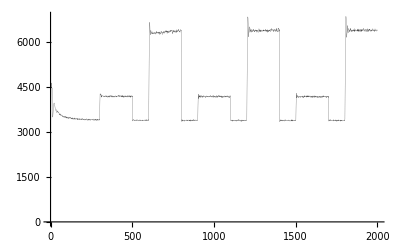

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.19,3822.29,5243.69,6254.41,6911.94,7125.4,7162.41,7087.01,6950.77,6898.24,6832.01,6751.66,6565.23,6236.87,5980.69,5634.25,5229.15,4814.02,4566.02,4444.42,4415.38,4387.13,4347.44,4344.56,4346.51,4306.67,4333.67,4279.12,4319.68,4367.47,4400.59,4388.17,4398.05,4402.44,4445.19,4439.79,4435.84,4464.17,4405.01,4445.16,4475.94,4408.15,4400.03,4366.56,4321.24,4314.21,4241.59,4162.45,4139.99,4067.18,4079.2,4057.13,4012.19,4033.93,3958.62,3956.74,3900.71,3873.36,3898.13,3876.33,3904.48,3807.2,3848.46,3862.57,3813.22,3800.15,3774.01,3761.89,3776.93,3730.12,3720.32,3707.82,3666.62,3637.65,3630.8,3620.49,3644.28,3605.1,3618.78,3597.42,3613.38,3591.48,3608.04,3575.82,3604.72,3566.67,3592.57,3590.86,3553.64,3561.47,3588.29,3556.92,3553.71,3552.04,3572.64,3579.58,3570.81,3549.42,3545.42,3568.5,3497.63,3577.71,3560.31,3530.95,3525.74,3529.57,3517.71,3511.79,3537.04,3493.4,3564.04,3497.08,3529.06,3543.75,3518.57,3519.02,3517.35,3501.59,3488.84,3511.09,3509.2,3521.34,3482.,3518.22,3524.05,3492.94,3497.62,3499.88,3467.27,3501.34,3498.88,3502.69,3528.96,3501.32,3481.64,3482.32,3456.93,3512.98,3512.64,3486.13,3468.56,3500.14,3474.32,3489.04,3476.45,3461.14,3478.47,3485.44,3492.28,3475.84,3493.68,3453.49,3500.42,3489.03,3497.26,3468.37,3481.21,3478.2,3466.99,3468.89,3471.6,3498.58,3488.3,3488.31,3449.37,3468.22,3502.59,3476.9,3466.71,3532.4,3428.63,3454.73,3481.24,3464.91,3454.6,3508.01,3447.38,3473.07,3493.16,3474.49,3482.09,3492.88,3457.54,3454.72,3504.36,3486.21,3486.38,3450.43,3485.48,3475.77,3480.73,3502.13,3480.06,3467.64,3469.03,3484.24,3508.22,3500.22,3460.02,3494.01,3474.1,3512.93,3463.02,3505.76,3493.54,3484.77,3475.81,3494.92,3448.08,3498.26,3440.41,3471.68,3492.04,3456.45,3506.32,3488.18,3488.89,3467.33,3473.13,3460.97,3475.69,3479.3,3481.17,3433.19,3473.75,3471.77,3451.6,3449.83,3498.77,3479.04,3459.43,3482.86,3462.68,3479.25,3495.11,3459.82,3488.64,3440.55,3437.76,3454.4,3470.51,3458.77,3473.69,3451.9,3464.94,3453.45,3466.55,3496.08,3480.33,3455.49,3465.03,3463.97,3454.28,3447.01,3478.85,3477.46,3481.49,3484.87,3473.67,3464.86,3473.96,3454.66,3432.99,3480.59,3465.12,3470.54,3450.19,3484.03,3449.54,3462.94,3463.63,3471.39,3457.11,3463.28,3489.71,3488.07,3455.98,3457.83,3493.16,3440.34,3431.92,3462.33,3417.8,3465.12,3469.46,3449.16,3463.37,3463.13,3453.38,3451.31,3444.11,3448.17,3492.7,3459.49,3464.73,3464.51,3439.08,3476.67,3480.29,3457.37,3447.08,3437.54,3473.84,3440.19,3476.02,3458.32,3418.79,3465.76,3462.31,3413.91,3483.37,3446.99,3434.79,3460.53,3429.97,3453.03,3458.84,3443.51,3415.18,3443.75,3428.99,3461.05,3449.88,3470.77,3451.07,3461.81,3444.27,3423.79,3459.41,3428.75,3443.48,3426.7,3467.93,3451.29,3460.13,3456.58,3426.06,3445.7,3431.46,3452.05,3448.98,3434.03,3471.46,3469.88,3456.6,3427.61,3471.56,3452.98,3438.06,3437.65,3479.13,3461.63,3451.98,3450.1,3485.26,3466.8,3419.49,3441.83,3449.97,3446.66,3476.74,3467.64,3414.68,3436.15,3467.66,3460.53,3434.46,3460.39,3475.45,3493.43,3441.67,3460.97,3488.02,3464.64,3438.53,3457.02,3468.71,3444.39,3433.88,3449.56,3433.47,3423.97,3485.96,3433.72,3465.35,3464.43,3459.88,3484.21,3488.75,3477.72,3445.99,3434.39,3451.05,3460.17,3475.34,3444.38,3458.8,3426.07,3453.55,3478.48,3461.32,3431.38,3439.62,3457.62,3451.07,3448.27,3445.29,3461.64,3476.43,3464.51,3451.98,3416.46,3446.99,3442.54,3469.49,3441.31,3460.94,3416.36,3467.49,3447.,3473.99,3458.2,3435.01,3484.47,3441.88,3451.25,3468.56,3434.1,3445.63,3469.72,3484.3,3429.17,3456.53,3456.43,3462.38,3453.06,3403.31,3463.32,3472.27,3447.65,3468.61,3461.92,3439.46,3440.6,3433.25,3466.32,3451.94,3463.28,3459.36,3461.3,3434.26,3451.82,3441.87,3424.4,3462.85,3437.97,3418.94,3455.58,3446.72,3482.81,3443.4,3450.72,3481.01,3429.96,3450.97,3479.89,3454.13,3457.15,3455.85,3473.37,3457.04,3432.48,3450.88,3456.68,3474.88,3469.02,3495.54,3450.17,3459.41,3440.4,3454.41,3423.06,3411.35,3459.43,3470.84,3436.88,3432.17,3429.53,3426.09,3452.7,3453.92,3444.99,3474.22,3479.62,3446.88,3432.92,3437.18,3452.48,3432.21,3436.51,3468.93,3471.53,3423.85,3436.64,3455.14,3411.68,3459.83,3451.34,3434.12,3426.72,3450.53,3448.76,3450.16,3452.15,3448.95,3452.43,3459.04,3437.14,3444.57,3457.19,3492.23,3459.46,3429.16,3452.57,3494.19,3435.,3428.45,3435.8,3428.67,3449.62,3462.21,3448.91,3434.99,3427.94,3439.41,3460.25,3466.05,3417.75,3422.27,3458.81,3437.85,3446.3,3426.79,3497.18,3446.74,3438.32,3458.93,3440.96,3454.78,3465.74,3451.5,3467.96,3461.01,3439.48,3450.64,3471.67,3442.89,3441.7,3434.03,3429.6,3478.81,3443.38,3436.41,3460.76,3438.4,3420.73,3445.2,3458.68,3441.91,3459.52,3468.64,3431.12,3464.18,3453.68,3442.15,3444.96,3457.43,3432.59,3432.86,3426.3,3426.64,3437.12,3485.75,3467.72,3434.75,3453.35,3447.42,3470.97,3431.93,3431.04,3456.69,3455.43,3479.03,3456.71,3440.55,3437.64,3444.01,3471.49,3424.24,3420.3,3414.68,3421.97,3450.17,3485.24,3448.48,3453.45,3450.14,3433.78,3451.12,3434.25,3424.88,3455.14,3428.39,3431.22,3472.07,3469.73,3458.35,3445.45,3474.33,3463.31,3482.29,3430.69,3433.17,3456.17,3450.19,3452.75,3437.41,3439.02,3477.6,3440.96,3440.38,3443.86,3444.02,3445.99,3497.93,3458.99,3447.18,3438.41,3468.61,3451.,3433.63,3464.01,3465.9,3431.3,3426.54,3469.49,3469.91,3421.58,3433.66,3472.94,3469.88,3422.61,3488.57,3451.14,3440.8,3431.83,3451.56,3454.29,3437.17,3460.92,3415.07,3440.08,3449.45,3461.77,3466.06,3444.19,3423.31,3448.52,3422.2,3449.37,3438.06,3434.15,3469.24,3433.56,3422.71,3443.37,3426.18,3463.64,3452.46,3446.74,3407.79,3445.37,3436.51,3462.26,3414.08,3455.14,3471.14,3432.46,3439.65,3451.35,3437.98,3460.98,3453.17,3418.17,3445.69,3437.47,3483.22,3480.4,3424.14,3456.52,3441.27,3444.26,3439.37,3439.4,3438.03,3452.72,3447.09,3453.72,3457.09,3446.79,3450.55,3425.49,3446.41,3446.37,3446.3,3456.09,3476.64,3448.83,3443.16,3462.43,3438.45,3422.91,3457.55,3458.11,3441.31,3456.85,3454.57,3439.23,3412.26,3426.44,3440.4,3421.73,3450.44,3432.86,3409.13,3425.97,3414.03,3456.6,3453.02,3434.04,3451.4,3431.97,3449.51,3425.38,3434.11,3475.02,3451.56,3449.87,3441.05,3459.95,3448.62,3463.87,3445.78,3453.77,3422.8,3446.83,3438.75,3439.43,3446.79,3442.16,3423.8,3421.41,3444.65,3445.9,3444.04,3450.25,3458.48,3441.29,3443.59,3427.88,3487.7,3452.29,3453.41,3466.9,3451.44,3428.05,3426.45,3440.43,3423.25,3468.95,3458.74,3462.87,3448.14,3453.04,3443.16,3438.22,3447.75,3437.6,3433.33,3444.36,3466.5,3432.81,3465.6,3442.46,3438.37,3473.32,3435.4,3443.65,3474.68,3457.72,3447.24,3463.8,3438.03,3443.06,3435.71,3468.7,3448.42,3439.46,3420.63,3428.97,3426.11,3462.01,3439.45,3431.36,3425.39,3447.73,3505.91,3416.63,3470.27,3495.99,3430.63,3428.72,3414.02,3457.88,3445.44,3433.89,3479.53,3437.46,3433.76,3429.15,3420.84,3459.76,3465.59,3470.14,3467.55,3434.37,3439.36,3458.21,3439.68,3458.2,3456.71,3468.06,3425.75,3473.67,3449.86,3419.41,3455.31,3446.19,3444.43,3457.26,3453.72,3446.31,3438.46,3431.45,3459.25,3442.55,3401.71,3441.49,3447.38,3418.27,3415.96,3463.17,3452.6,3437.43,3454.78,3436.63,3458.14,3452.3,3451.38,3431.15,3442.28,3432.37,3459.26,3410.9,3459.4,3454.32,3454.32,3418.23,3451.66,3458.24,3423.99,3467.67,3456.62,3448.28,3451.,3455.52,3443.23,3447.1,3441.37,3431.21,3448.03,3429.47,3471.25,3438.61,3428.08,3442.03,3452.45,3434.21,3435.03,3432.71,3460.13,3433.23,3425.78,3446.59,3453.11,3464.58,3474.95,3433.5,3430.09,3422.17,3475.89,3412.33,3474.82,3460.86,3452.25,3447.36,3472.22,3458.22,3476.36,3457.77,3419.68,3446.24,3450.82,3431.15,3448.06,3418.1,3439.01,3428.76,3453.16,3459.47,3421.88,3433.12,3475.27,3453.54,3454.42,3429.9,3429.13,3449.02,3438.9,3471.44,3432.68,3446.11,3425.79,3449.45,3453.76,3409.17,3474.52,3437.43,3420.65,3439.7,3420.1,3412.85,3431.79,3431.21,3418.09,3464.66,3438.83,3431.13,3438.5,3424.42,3459.84,3425.23,3433.53,3439.37,3438.47,3473.67,3430.83,3427.57,3423.3,3473.01,3461.68,3424.42,3441.17,3469.24,3455.08,3458.85,3429.44,3441.37,3420.38,3441.42,3433.86,3435.3,3408.91,3451.17,3434.7,3428.89,3460.16,3445.01,3451.55,3474.8,3430.57,3442.47,3441.78,3450.86,3411.62,3441.78,3446.52,3421.12,3473.66,3439.6,3431.28,3456.57,3443.49,3452.16,3445.2,3452.09,3463.78,3443.08,3463.36,3427.52,3441.96,3445.85,3424.78,3438.46,3469.75,3438.62,3450.68,3450.07,3463.18,3458.76,3446.7,3441.08,3436.49,3448.54,3433.44,3456.56,3413.32,3450.25,3465.21,3434.5,3440.71,3465.27,3468.11,3458.14,3453.13,3450.47,3452.65,3429.97,3443.61,3481.86,3453.21,3461.89,3466.6,3455.8,3421.42,3457.7,3449.72,3453.37,3438.49,3452.41,3446.31,3457.39,3439.47,3413.6,3443.24,3455.62,3446.14,3451.71,3413.28,3441.62,3462.32,3452.47,3457.14,3454.2,3431.76,3449.07,3461.25,3454.17,3460.9,3434.26,3473.31,3438.35,3447.54,3448.39,3469.05,3425.58,3453.03,3414.68,3457.19,3477.77,3448.79,3430.61,3424.52,3437.37,3442.25,3465.6,3455.48,3431.69,3425.08,3432.89,3446.05,3427.76,3441.48,3455.16,3450.01,3431.15,3429.27,3442.97,3445.24,3449.31,3438.57,3445.93,3461.04,3453.46,3450.73,3454.26,3425.55,3449.56,3475.15,3459.13,3420.02,3469.91,3405.1,3419.18,3451.43,3450.16,3456.01,3445.04,3465.59,3423.05,3462.77,3437.19,3427.4,3474.08,3479.09,3437.3,3449.27,3445.09,3436.02,3461.02,3465.71,3458.41,3427.44,3443.16,3433.3,3414.89,3450.77,3434.66,3423.94,3446.37,3432.44,3482.78,3449.52,3422.72,3489.91,3464.65,3425.38,3454.92,3442.05,3425.53,3444.59,3436.57,3441.86,3451.18,3439.78,3473.26,3439.13,3451.,3449.43,3460.81,3429.91,3458.76,3448.8,3415.11,3430.2,3473.06,3426.4,3424.88,3436.13,3458.78,3443.32,3440.6,3435.56,3445.23,3442.61,3449.86,3429.48,3448.51,3440.21,3446.32,3437.62,3456.14,3432.33,3431.49,3450.21,3465.88,3385.55,3437.28,3474.46,3440.48,3447.76,3443.77,3450.93,3446.,3470.49,3430.17,3400.28,3429.71,3451.74,3448.66,3426.15,3464.15,3447.41,3461.01,3448.75,3441.83,3460.22,3457.63,3423.06,3444.49,3460.8,3432.94,3432.57,3447.87,3443.18,3444.94,3470.43,3457.,3459.94,3426.74,3436.33,3477.23,3455.39,3422.67,3452.28,3454.16,3430.85,3434.41,3431.11,3407.35,3455.18,3432.54,3473.67,3436.9,3445.5,3437.87,3440.29,3435.27,3442.53,3447.2,3453.67,3438.6,3412.11,3429.07,3445.72,3462.48,3416.79,3457.55,3453.45,3453.18,3427.13,3453.12,3443.43,3434.05,3451.82,3459.49,3434.47,3443.02,3443.43,3476.05,3474.5,3458.59,3456.17,3452.44,3428.65,3428.74,3470.77,3465.78,3431.74,3443.89,3437.05,3472.75,3416.49,3416.46,3435.29,3413.09,3410.79,3456.72,3462.2,3454.78,3424.57,3435.35,3438.33,3425.34,3447.32,3435.52,3444.05,3435.62,3463.5,3454.84,3434.75,3443.48,3444.1,3430.97,3455.59,3437.79,3457.52,3438.98,3448.85,3456.91,3472.7,3444.51,3432.2,3433.18,3471.67,3432.44,3438.2,3411.5,3453.31,3415.92,3429.53,3464.88,3455.97,3468.08,3437.16,3416.89,3440.86,3461.82,3441.96,3458.28,3432.75,3478.34,3423.62,3425.61,3450.94,3424.03,3421.85,3453.83,3447.6,3412.4,3441.47,3445.02,3436.21,3426.77,3497.38,3432.88,3402.17,3440.99,3427.52,3440.56,3448.85,3442.16,3417.24,3469.52,3417.97,3463.98,3428.99,3444.84,3439.62,3422.16,3433.74,3450.8,3447.38,3411.42,3455.,3459.7,3449.22,3448.53,3419.59,3422.99,3447.05,3431.05,3450.32,3447.09,3439.41,3478.82,3462.07,3427.12,3441.59,3464.87,3441.52,3456.96,3442.42,3414.78,3467.08,3458.14,3441.03,3447.57,3430.98,3441.04,3471.47,3445.48,3435.39,3409.76,3468.99,3433.13,3459.55,3434.86,3447.31,3455.19,3447.8,3460.45,3413.17,3428.63,3465.94,3465.6,3442.73,3459.19,3447.15,3444.74,3449.17,3437.89,3430.74,3446.17,3438.3,3449.08,3448.49,3444.26,3444.6,3435.52,3437.45,3459.49,3447.76,3466.84,3453.06,3435.73,3465.2,3445.88,3432.02,3458.35,3458.7,3413.2,3459.49,3435.86,3460.82,3428.17,3440.79,3431.22,3465.93,3455.41,3471.44,3474.62,3458.4,3438.94,3441.06,3463.74,3419.92,3445.95,3439.34,3454.88,3455.28,3423.64,3442.34,3446.42,3431.21,3460.,3435.75,3433.76,3418.32,3432.55,3449.94,3460.64,3467.7,3465.75,3437.06,3468.96,3451.53,3437.,3469.88,3429.18,3427.02,3421.44,3414.89,3457.1,3433.54,3438.63,3433.16,3407.23,3440.66,3425.97,3451.86,3443.64,3395.75,3465.57,3454.33,3440.8,3460.72,3445.95,3447.08,3426.49,3458.48,3424.27,3441.82,3443.61,3432.98,3468.12,3445.1,3436.76,3451.01,3460.67,3458.88,3434.47,3437.87,3465.71,3436.78,3461.87,3432.7,3448.76,3420.63,3430.77,3459.18,3474.4,3411.8,3425.37,3442.83,3452.45,3435.61,3441.72,3465.99,3443.31,3483.7,3448.42,3433.77,3433.03,3448.96,3436.78,3425.71,3459.21,3442.5,3460.03,3443.23,3469.57,3470.95,3430.52,3427.05,3448.82,3442.09,3442.7,3458.64,3446.56,3432.58,3440.56,3414.25,3438.91,3448.27,3440.23,3438.18,3455.13,3454.22,3439.18,3455.94,3431.49,3451.21,3457.3,3441.43,3449.61,3469.96,3484.42,3472.12,3435.64,3467.5,3436.95,3433.81,3462.66,3455.56,3451.67,3464.31,3444.81,3429.18,3464.99,3431.11,3422.65,3415.36,3430.98,3433.46,3410.73,3442.32,3440.79,3424.01,3411.77,3428.67,3462.06,3445.19,3439.09,3440.71,3450.04,3444.3,3470.97,3438.39,3455.61,3456.52,3463.24,3424.09,3467.82,3431.2,3441.59,3453.19,3465.17,3425.14,3458.47,3450.32,3434.87,3453.83,3422.7,3436.37,3448.97,3445.76,3401.91,3442.12,3458.21,3424.79,3446.35,3448.24,3447.9,3420.93,3434.47,3430.45,3461.8,3445.45,3448.65,3431.81,3455.7,3452.33,3428.54,3449.21,3456.64,3447.78,3431.7,3432.8,3455.39,3452.01,3427.97,3445.75,3450.14,3411.54,3438.07,3448.01,3444.44,3447.54,3453.01,3454.33,3450.08,3403.02,3418.25,3425.36,3415.79,3441.58,3445.62,3459.42,3463.41,3452.27,3458.26,3448.66,3439.18,3447.72,3426.86,3451.15,3467.93,3462.02,3451.82,3426.27,3444.26,3465.05,3439.96,3426.69,3432.97,3448.21,3489.79,3442.33,3409.47,3445.56,3437.91,3453.67,3449.27,3444.88,3438.99,3436.96,3441.29,3442.86,3446.52,3436.27,3453.32,3448.04,3468.32,3483.92,3459.78,3426.48,3459.03,3442.32,3455.35,3434.3,3468.12,3427.19,3434.91,3472.53,3469.74,3436.89,3436.47,3449.27,3445.6,3439.7,3457.89,3448.11,3438.66,3452.37,3471.1,3450.66,3419.76,3426.23,3448.51,3449.12,3414.07,3429.02,3444.21,3434.76,3430.25,3405.86,3449.84,3436.81,3458.12,3443.01,3458.85,3439.84,3416.79,3425.02,3452.08,3422.92,3443.96,3423.72,3449.61,3441.78,3431.61,3450.15,3466.6,3480.35,3458.63,3460.31,3479.81,3462.7,3433.52,3441.79,3420.73,3452.74,3465.83,3444.21,3443.76,3444.76,3456.59,3428.26,3454.98,3422.82,3436.84,3400.34,3443.,3428.29,3416.78,3431.56,3432.94,3434.51,3467.58,3450.89,3413.32,3453.86,3445.9,3445.77,3444.93,3398.53,3503.64,3444.03,3433.91,3433.84,3436.63,3421.99,3461.99,3458.71,3429.26,3442.8,3440.89,3435.68,3438.83,3467.58,3450.7,3418.16,3450.27,3435.99,3420.18,3427.33,3460.56,3451.29,3440.93,3435.01,3433.19,3468.06,3436.85,3414.44,3429.38,3456.42,3473.43,3450.52,3447.46,3456.8,3441.01,3441.28,3427.94,3446.34,3438.79,3430.95,3454.3,3402.78,3432.42,3420.73,3442.58,3431.34,3413.55,3426.88,3441.91,3465.34,3442.1,3466.47,3443.16,3431.18,3455.91,3428.41,3426.12,3438.68,3429.49,3425.9,3443.44,3455.02,3436.46,3461.57,3424.01,3438.36,3419.32,3418.88,3445.99,3423.25,3419.73,3426.55,3442.16,3431.39,3447.33,3453.62,3421.,3446.43,3413.17,3414.88,3442.36,3463.76,3416.1,3433.92,3428.9,3427.37,3444.58,3433.09,3450.42,3423.39,3428.43,3470.05,3437.6,3461.34,3446.29,3421.29,3461.6,3424.51,3464.16,3463.03,3436.02,3449.54,3437.59,3445.41,3441.12,3438.47,3418.69,3419.62,3404.61,3439.45,3445.35,3446.59,3458.33,3435.69,3464.66,3426.68,3414.29,3439.98,3447.8,3417.96,3439.77,3435.63,3444.65,3434.42,3449.44,3399.55,3430.06,3450.14,3439.6,3440.94,3434.94,3457.,3424.72,3437.6,3459.4,3471.36,3450.63,3429.55,3439.54,3458.79,3407.53,3441.33,3426.,3419.5,3436.71,3448.1,3452.27,3461.52,3444.35,3445.18,3434.98,3449.53,3427.16,3438.47,3449.48,3451.32,3441.59,3444.39,3438.29,3452.46,3425.4,3455.37,3434.65,3414.49,3435.,3468.22,3441.08,3433.68,3428.15,3453.7,3424.,3431.7,3422.92,3440.14,3440.61,3449.87,3452.97,3425.08,3397.8,3449.77,3449.19,3427.19,3424.26,3395.58,3444.81,3441.21,3426.36,3438.65,3436.23,3471.35,3454.74,3441.89,3429.7,3460.27,3446.63,3470.49,3452.89,3467.89,3407.43,3420.58,3446.33,3443.26,3450.38,3431.78,3421.32,3434.02,3467.65,3437.35,3418.64,3462.38,3444.49,3419.06,3434.98,3438.73,3416.47,3453.57,3456.75,3443.41,3462.49,3448.89,3435.65,3451.05,3420.25,3443.87,3419.68,3442.01,3450.72,3430.36,3406.75,3430.56,3425.74,3458.4,3434.59,3444.11,3428.64,3474.31,3433.68,3435.67,3416.52,3426.97,3450.4,3437.68,3458.23},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.09,3239.05,3694.99,3703.93,3568.68,3561.72,3609.72,3586.57,3570.75,3574.53,3600.31,3570.95,3580.82,3592.68,3612.77,3579.73,3584.88,3602.3,3630.74,3598.03,3599.05,3646.24,3619.26,3597.32,3632.,3587.66,3580.,3560.39,3582.46,3586.5,3560.87,3592.39,3609.93,3586.33,3591.82,3556.05,3592.5,3591.94,3595.36,3584.01,3608.81,3597.67,3607.7,3593.21,3619.46,3590.11,3617.25,3599.88,3611.97,3576.46,3604.32,3577.62,3598.19,3584.94,3585.21,3589.38,3609.6,3585.72,3587.29,3580.37,3610.01,3586.57,3585.22,3585.42,3584.15,3558.85,3577.91,3564.29,3597.92,3595.45,3595.83,3552.32,3573.02,3580.55,3599.71,3581.61,3567.23,3574.29,3580.46,3614.36,3594.16,3564.43,3589.15,3563.56,3555.03,3606.38,3567.32,3563.35,3613.09,3567.97,3570.48,3579.04,3588.02,3587.07,3566.04,3609.39,3590.27,3571.03,3565.98,3619.38,3609.47,3547.9,3601.64,3585.35,3592.76,3602.67,3578.9,3585.28,3614.39,3578.93,3585.69,3549.49,3596.58,3604.97,3578.35,3545.33,3571.41,3577.45,3538.39,3586.68,3621.61,3590.17,3594.84,3559.95,3590.78,3584.11,3568.84,3597.78,3570.96,3587.9,3591.9,3607.96,3591.97,3601.82,3573.84,3586.86,3603.79,3600.67,3587.8,3575.36,3562.25,3606.37,3589.47,3557.97,3600.88,3570.9,3588.18,3598.94,3597.25,3612.05,3595.91,3617.64,3619.56,3609.93,3594.86,3553.78,3587.15,3592.88,3609.25,3583.03,3580.72,3582.96,3573.6,3603.12,3575.22,3599.44,3555.81,3587.78,3608.97,3595.97,3607.58,3590.18,3579.62,3579.33,3608.55,3628.03,3607.98,3572.85,3611.48,3586.14,3581.47,3607.2,3615.79,3590.93,3609.35,3575.33,3587.29,3586.93,3562.09,3593.48,3580.4,3607.93,3581.19,3619.57,3628.59,3606.83,3591.7,3580.02,3579.77,3570.11,3579.49,3581.39,3569.67,3632.06,3569.59,3575.88,3604.78,3596.15,3604.57,3572.92,3566.7,3573.47,3601.29,3575.45,3609.03,3583.21,3571.69,3553.92,3604.19,3615.87,3574.98,3596.17,3565.36,3564.22,3560.51,3620.08,3582.89,3577.03,3591.93,3594.58,3621.35,3572.4,3615.49,3575.58,3579.97,3580.44,3582.94,3567.13,3581.57,3596.5,3561.84,3571.46,3594.99,3570.37,3580.48,3583.56,3585.79,3591.2,3587.63,3601.28,3604.92,3632.42,3620.84,3591.75,3579.61,3542.23,3582.31,3602.65,3588.71,3592.1,3583.42,3599.05,3602.33,3589.15,3631.5,3580.88,3565.74,3599.34,3595.39,3616.94,3608.49,3561.34,3583.63,3588.3,3573.54,3594.42,3609.17,3616.89,3625.57,3622.,3601.6,3565.56,3590.7,3628.28,3607.95,3607.56,3604.52,3590.09,3582.93,3577.85,3564.35,3570.46,3621.02,3576.32,3592.05,3588.62,3634.55,3581.64,3581.2,3591.57,3596.05,3578.53,3581.64,3586.37,3639.73,3592.32,3574.06,3586.8,3617.49,3599.69,3568.02,3593.51,3561.91,3590.09,3540.68,3588.62,3604.38,3582.94,3600.69,3599.57,3611.8,3610.02,3612.58,3571.66,3603.73,3605.8,3600.78,3555.85,3584.03,3599.98,3582.68,3584.48,3599.01,3590.13,3596.58,3606.15,3577.28,3572.99,3590.1,3569.06,3578.99,3594.96,3603.98,3598.16,3588.41,3591.96,3618.37,3620.6,3587.73,3573.48,3585.3,3584.,3592.13,3593.81,3608.96,3595.06,3562.6,3580.1,3609.26,3597.93,3573.5,3582.5,3607.12,3571.9,3591.35,3602.87,3580.75,3555.34,3613.51,3597.28,3585.49,3583.28,3604.14,3582.03,3586.1,3596.63,3601.1,3564.19,3585.63,3595.74,3639.6,3607.36,3621.44,3594.16,3627.25,3583.46,3577.64,3581.05,3556.89,3578.7,3588.56,3620.43,3604.84,3609.49,3588.8,3611.56,3637.63,3626.9,3591.48,3579.73,3572.61,3562.47,3606.72,3591.81,3589.79,3613.16,3574.06,3570.31,3589.98,3604.17,3600.77,3565.1,3560.78,3566.92,3579.37,3576.17,3566.92,3562.22,3587.31,3563.82,3591.34,3612.,3577.28,3599.37,3590.42,3587.47,3601.11,3596.34,3562.45,3599.44,3588.61,3577.21,3600.79,3569.82,3600.66,3582.64,3588.72,3588.32,3591.17,3582.7,3612.1,3594.56,3582.4,3624.83,3595.52,3595.17,3571.28,3593.55,3560.56,3616.94,3581.83,3569.98,3594.92,3588.31,3597.98,3578.25,3564.83,3601.69,3608.94,3585.48,3580.63,3580.62,3580.42,3591.3,3581.14,3585.13,3622.21,3595.95,3612.65,3593.5,3616.42,3601.32,3585.11,3624.24,3607.62,3622.66,3580.61,3578.73,3560.75,3605.52,3604.87,3571.88,3573.87,3586.99,3581.44,3603.3,3597.68,3618.39,3613.85,3610.69,3591.57,3580.86,3579.03,3608.7,3546.59,3562.03,3587.35,3583.99,3595.56,3560.71,3561.15,3606.86,3596.08,3582.66,3560.69,3607.05,3606.93,3563.75,3578.3,3565.47,3563.27,3551.73,3596.06,3616.84,3611.46,3608.54,3578.63,3595.82,3573.41,3616.19,3577.25,3566.63,3585.93,3554.42,3587.66,3597.79,3587.42,3586.87,3627.99,3593.9,3595.45,3589.42,3562.57,3614.68,3568.54,3581.2,3567.89,3594.07,3614.64,3572.79,3609.11,3600.95,3590.23,3570.5,3536.69,3584.45,3567.25,3615.08,3599.61,3613.04,3609.22,3576.42,3554.02,3594.59,3574.4,3571.79,3598.06,3564.13,3570.01,3590.17,3558.41,3556.85,3598.29,3584.49,3618.85,3588.71,3590.83,3569.43,3598.49,3597.17,3593.08,3597.06,3598.04,3578.68,3603.69,3592.3,3569.44,3584.32,3573.45,3598.93,3590.93,3595.06,3610.47,3595.79,3585.13,3524.,3572.62,3571.74,3608.55,3573.52,3555.28,3596.05,3562.71,3571.01,3587.65,3565.3,3538.08,3570.16,3572.44,3559.9,3569.37,3590.52,3573.34,3569.15,3578.09,3577.51,3545.57,3571.89,3609.17,3581.37,3572.31,3583.73,3632.19,3571.59,3596.34,3596.38,3615.05,3589.19,3579.91,3586.9,3570.78,3569.11,3600.47,3584.78,3607.13,3608.24,3598.05,3588.25,3586.65,3588.26,3570.27,3606.69,3579.89,3606.,3571.67,3575.54,3605.46,3574.11,3567.69,3558.96,3582.39,3567.17,3612.74,3593.88,3573.98,3559.82,3592.15,3604.47,3577.62,3615.41,3593.51,3571.06,3615.02,3613.66,3597.32,3566.66,3567.13,3619.42,3592.73,3571.05,3586.53,3581.51,3579.5,3599.12,3571.02,3581.6,3571.21,3571.55,3578.06,3594.31,3590.55,3563.26,3602.64,3574.18,3578.,3601.56,3566.11,3587.28,3580.32,3584.06,3610.24,3600.27,3546.24,3590.28,3630.07,3599.18,3562.75,3607.93,3575.75,3570.7,3567.98,3603.27,3605.33,3631.64,3568.87,3599.13,3575.49,3602.02,3574.01,3578.78,3592.54,3591.35,3616.78,3569.12,3581.45,3611.21,3566.63,3592.79,3589.2,3572.18,3592.53,3585.66,3567.1,3555.55,3589.04,3632.93,3559.75,3625.6,3586.08,3565.52,3608.37,3601.77,3593.1,3593.84,3593.97,3561.53,3596.42,3570.92,3607.45,3575.16,3574.86,3576.93,3585.45,3586.31,3591.43,3586.21,3604.13,3612.18,3597.54,3554.31,3601.21,3581.03,3603.14,3624.75,3610.57,3559.05,3586.33,3600.74,3602.79,3591.29,3581.27,3595.1,3586.39,3590.83,3594.95,3605.43,3571.68,3615.93,3589.72,3552.1,3574.95,3580.13,3580.76,3595.01,3585.51,3553.12,3570.62,3599.84,3585.34,3591.12,3600.39,3596.98,3558.08,3574.27,3581.45,3583.38,3565.69,3583.15,3586.78,3581.04,3578.63,3565.11,3557.08,3581.56,3584.23,3567.74,3563.03,3596.85,3606.52,3582.73,3607.49,3599.98,3576.65,3604.14,3628.02,3592.93,3567.81,3590.22,3611.7,3610.12,3629.54,3605.69,3614.06,3604.94,3585.46,3571.34,3549.17,3597.81,3587.88,3615.41,3603.01,3597.26,3586.6,3596.05,3578.11,3584.04,3581.69,3595.96,3596.,3590.09,3604.89,3598.56,3597.22,3587.34,3581.46,3608.37,3580.4,3578.,3581.66,3603.65,3576.77,3580.46,3580.36,3573.95,3580.18,3611.05,3600.05,3577.94,3598.77,3568.7,3575.07,3588.18,3603.62,3590.1,3583.63,3618.6,3579.25,3613.98,3576.39,3594.11,3588.57,3578.97,3590.89,3585.8,3587.13,3596.89,3583.68,3579.37,3570.24,3597.22,3583.36,3588.85,3569.46,3563.8,3586.48,3565.08,3560.37,3550.71,3584.27,3554.67,3589.34,3615.36,3613.25,3590.55,3595.77,3603.72,3575.28,3589.37,3583.61,3621.31,3555.07,3626.23,3593.26,3612.46,3581.87,3606.58,3605.87,3569.98,3559.19,3585.73,3614.26,3586.76,3585.54,3591.3,3571.1,3592.48,3576.04,3588.83,3589.49,3568.12,3585.7,3605.04,3573.85,3601.47,3565.88,3610.24,3596.35,3622.93,3589.79,3560.13,3610.5,3614.82,3616.39,3595.9,3570.97,3569.39,3621.52,3599.11,3578.75,3582.56,3602.91,3576.37,3631.26,3617.67,3592.34,3567.81,3593.64,3584.28,3577.01,3570.93,3591.69,3586.02,3568.34,3593.2,3567.16,3591.37,3597.31,3582.09,3585.36,3615.12,3602.8,3588.5,3601.5,3605.04,3584.7,3602.54,3596.83,3615.94,3607.6,3612.84,3614.41,3583.7,3612.69,3579.14,3569.95,3593.88,3583.03,3598.05,3646.44,3588.4,3599.62,3610.24,3590.45,3575.77,3585.13,3585.39,3574.4,3572.16,3558.07,3575.5,3606.19,3619.81,3586.76,3577.15,3612.38,3600.69,3599.39,3580.75,3584.02,3571.6,3561.01,3600.72,3616.3,3588.39,3579.24,3586.54,3612.2,3583.83,3577.91,3580.31,3581.38,3608.8,3605.52,3578.63,3582.42,3598.95,3583.63,3574.55,3595.39,3611.67,3602.69,3616.08,3598.79,3571.17,3567.12,3600.84,3596.36,3603.21,3584.33,3602.63,3595.15,3581.19,3609.39,3611.38,3633.28,3594.31,3557.94,3590.68,3600.12,3576.65,3568.45,3554.12,3595.98,3612.96,3600.03,3577.01,3573.25,3597.64,3573.65,3583.64,3599.71,3586.75,3616.93,3612.17,3587.76,3611.38,3587.94,3585.07,3595.34,3580.85,3566.12,3585.86,3591.39,3603.52,3594.13,3584.04,3595.8,3627.99,3617.84,3610.1,3562.87,3607.98,3597.75,3586.5,3596.2,3597.74,3584.38,3608.56,3589.15,3609.49,3573.56,3576.29,3618.59,3617.06,3612.48,3579.87,3614.79,3622.49,3595.67,3577.7,3585.59,3612.28,3613.32,3571.82,3554.1,3569.48,3586.33,3562.93,3575.18,3613.08,3604.79,3616.25,3590.37,3599.28,3578.08,3592.4,3578.26,3545.51,3586.73,3609.6,3568.26,3568.58,3564.55,3563.49,3561.75,3610.22,3593.22,3601.17,3587.54,3546.06,3577.57,3583.18,3620.08,3588.61,3600.23,3601.99,3617.02,3598.52,3598.82,3584.02,3598.01,3592.02,3621.62,3594.24,3583.81,3588.66,3582.12,3587.8,3613.39,3623.67,3568.83,3576.67,3590.2,3579.38,3589.47,3591.05,3590.73,3588.85,3599.11,3576.19,3598.97,3577.83,3592.99,3597.25,3571.8,3578.94,3592.09,3558.5,3574.76,3596.43,3585.22,3590.84,3576.85,3611.28,3634.96,3576.33,3591.32,3565.93,3607.64,3559.78,3593.48,3607.76,3581.18,3579.52,3593.64,3573.08,3594.85,3602.3,3577.47,3576.58,3621.84,3603.75,3610.33,3572.93,3607.88,3586.71,3565.51,3602.18,3597.8,3594.16,3606.22,3605.84,3559.72,3597.91,3615.36,3563.49,3584.39,3579.28,3607.47,3566.53,3587.8,3596.7,3598.65,3592.26,3562.22,3593.36,3557.95,3565.73,3601.04,3607.94,3590.98,3584.97,3566.11,3587.93,3612.77,3598.63,3602.36,3618.57,3588.77,3554.99,3635.73,3578.96,3602.28,3599.4,3583.26,3601.26,3568.81,3615.46,3566.57,3557.22,3598.16,3565.21,3551.51,3582.34,3574.3,3580.68,3593.56,3556.42,3596.11,3594.58,3590.97,3614.36,3637.01,3611.55,3567.85,3621.02,3577.2,3568.74,3606.02,3606.25,3616.23,3609.39,3570.21,3565.58,3573.38,3582.93,3598.6,3590.14,3584.14,3552.75,3603.31,3603.02,3579.54,3588.73,3591.94,3565.13,3616.28,3587.24,3588.37,3598.47,3621.16,3628.25,3587.17,3620.23,3586.44,3596.32,3596.17,3598.62,3614.05,3570.63,3542.78,3570.61,3577.28,3547.37,3598.92,3588.03,3572.59,3571.94,3590.25,3585.58,3594.33,3601.32,3585.05,3575.84,3584.04,3587.64,3573.44,3640.18,3629.76,3557.32,3609.94,3585.96,3579.09,3563.,3607.81,3603.92,3640.34,3600.37,3614.98,3584.04,3591.2,3587.98,3529.32,3598.3,3560.92,3591.26,3581.96,3597.25,3568.06,3563.63,3594.21,3566.43,3620.29,3620.44,3611.16,3631.08,3596.5,3566.81,3576.36,3620.59,3599.04,3583.,3582.41,3574.36,3552.51,3589.27,3580.32,3619.,3611.21,3594.13,3571.68,3592.56,3603.36,3602.65,3603.83,3600.9,3606.1,3588.16,3562.88,3615.9,3606.6,3563.08,3627.96,3597.52,3579.85,3589.95,3573.99,3594.08,3602.29,3613.29,3638.25,3598.14,3595.46,3583.11,3596.72,3613.77,3603.2,3570.73,3623.46,3629.38,3588.99,3612.3,3614.93,3605.14,3630.51,3621.48,3557.71,3566.6,3567.29,3577.31,3598.04,3616.64,3611.79,3589.84,3595.7,3593.42,3565.17,3584.91,3591.61,3583.17,3585.85,3604.79,3601.14,3559.43,3588.47,3580.48,3572.99,3598.85,3592.39,3576.05,3597.51,3584.58,3585.12,3613.42,3609.89,3571.25,3637.42,3633.68,3581.84,3587.3,3579.16,3575.96,3600.19,3592.22,3591.55,3604.8,3607.46,3599.07,3583.05,3586.83,3596.33,3594.76,3600.72,3598.42,3596.78,3584.69,3565.56,3586.84,3622.93,3582.54,3589.01,3597.14,3614.53,3587.86,3600.39,3560.06,3557.08,3606.61,3588.64,3573.74,3577.56,3577.1,3582.63,3573.65,3571.63,3577.3,3578.86,3597.9,3566.3,3582.31,3621.84,3564.68,3599.87,3577.04,3579.32,3589.96,3623.28,3588.93,3599.96,3590.41,3567.19,3611.52,3606.11,3589.94,3603.62,3620.27,3607.38,3585.55,3594.19,3609.47,3585.36,3622.33,3612.09,3615.97,3606.48,3610.27,3622.71,3554.44,3590.75,3592.95,3596.76,3603.25,3583.28,3584.92,3605.91,3563.47,3635.43,3579.59,3583.3,3592.43,3578.53,3600.93,3620.46,3592.75,3580.47,3601.45,3612.58,3577.32,3640.23,3612.,3632.73,3594.11,3600.48,3587.88,3602.99,3608.67,3583.09,3577.06,3582.45,3605.07,3583.96,3626.42,3568.5,3602.89,3582.83,3587.49,3590.16,3639.16,3597.68,3600.79,3573.94,3578.2,3591.4,3613.6,3598.9,3596.09,3594.49,3600.46,3579.74,3588.67,3589.46,3602.14,3608.16,3587.72,3550.94,3568.99,3572.33,3601.27,3583.48,3568.48,3585.1,3606.62,3615.78,3602.19,3610.34,3605.33,3573.29,3610.58,3560.67,3608.57,3597.17,3545.95,3586.97,3545.3,3595.26,3586.91,3547.58,3583.09,3585.81,3593.12,3604.7,3610.32,3582.98,3558.72,3565.95,3566.97,3595.14,3591.87,3558.73,3600.67,3594.47,3601.26,3568.45,3606.65,3570.47,3631.71,3593.62,3592.29,3595.68,3612.88,3579.28,3592.15,3601.78,3597.99,3611.34,3581.26,3559.55,3546.58,3593.95,3585.25,3588.04,3605.13,3585.83,3625.12,3584.34,3589.75,3569.76,3574.72,3602.26,3602.83,3575.09,3601.37,3549.98,3593.12,3616.43,3591.08,3569.44,3577.5,3579.22,3583.79,3562.7,3570.32,3600.36,3586.64,3531.06,3587.32,3566.51,3579.74,3622.4,3604.09,3597.76,3608.92,3568.95,3601.79,3603.88,3602.23,3557.05,3550.72,3563.61,3569.09,3570.41,3595.88,3606.82,3585.02,3591.18,3574.41,3557.43,3589.71,3620.75,3577.2,3570.28,3575.11,3575.38,3617.59,3586.45,3571.45,3610.49,3572.75,3579.34,3602.48,3608.71,3570.95,3623.64,3596.79,3587.22,3570.85,3620.97,3568.37,3589.,3637.88,3587.19,3564.32,3604.94,3585.28,3579.04,3605.28,3588.3,3577.75,3598.8,3577.84,3581.08,3600.35,3597.38,3581.82,3592.92,3586.37,3560.85,3601.53,3593.57,3585.3,3567.28,3594.96,3578.35,3594.47,3585.68,3598.65,3564.71,3591.62,3578.68,3575.87,3591.21,3574.56,3629.35,3563.17,3612.81,3576.04,3622.68,3586.66,3589.4,3605.96,3605.53,3569.76,3602.36,3577.17,3560.1,3573.69,3570.25,3569.97,3580.52,3617.75,3553.86,3578.13,3576.92,3585.25,3568.79,3590.23,3582.04,3565.63,3602.1,3599.87,3634.33,3574.89,3570.72,3607.99,3591.97,3590.1,3575.84,3585.18,3576.69,3577.62,3607.01,3594.3,3584.81,3569.5,3568.22,3573.04,3578.25,3637.87,3609.86,3541.72,3605.32,3591.24,3574.98,3590.4,3573.7,3600.95,3580.85,3585.32,3570.21,3570.35,3540.88,3598.88,3577.1,3596.54,3601.06,3587.19,3605.21,3578.3,3566.12,3587.48,3552.79,3554.68,3576.52,3572.89,3577.38,3610.46,3609.47,3618.38,3609.01,3606.43,3574.34,3622.46,3594.62,3610.43,3576.03,3601.25,3630.33,3606.03,3612.54,3588.61,3585.32,3560.04,3574.44,3578.22,3601.16,3577.9,3581.62,3592.36,3587.41,3589.93,3605.93,3600.91,3620.47,3646.96,3568.62,3606.25,3558.87,3546.02,3583.3,3590.8,3589.1,3574.79,3577.84,3575.55,3574.67,3595.46,3608.45,3580.3,3575.76,3594.32,3612.11,3632.02,3588.49,3602.96,3563.5,3578.73,3570.1,3592.74,3586.65,3569.29,3572.96,3574.96,3590.73,3602.23,3620.73,3573.58,3605.48,3583.49,3592.33,3579.,3580.57,3608.47,3620.56,3585.27,3576.35,3601.23,3574.22,3550.04,3601.21,3591.42,3618.83,3610.16,3596.87,3580.33,3608.65,3583.23,3569.56,3629.53,3572.73,3604.2,3610.73,3554.25,3579.32,3596.14,3602.2,3584.79,3580.78,3570.66,3564.21,3594.54,3586.91,3594.92,3629.85,3584.18,3624.59,3591.09,3575.88,3601.9,3609.63,3569.29,3563.44,3584.57,3606.03,3558.11,3527.43,3605.67,3596.03,3599.39,3595.59,3590.45,3582.86,3581.52,3593.5,3585.74,3595.29,3624.04,3616.87,3611.88,3587.04,3571.07,3598.96,3569.28,3597.59,3635.12,3584.34,3603.09,3595.58,3573.91,3605.33,3630.32,3616.5,3613.27,3591.3,3584.91,3579.58,3578.14,3598.89,3656.67,3599.15,3556.86,3606.93,3562.,3564.72,3575.85,3594.31,3573.83,3601.54,3583.6,3535.99,3554.14,3607.93,3603.27,3581.98,3565.05,3575.88,3544.05,3571.44,3605.4,3541.97,3555.19,3600.1,3585.63,3595.02,3606.98,3601.42,3616.95,3611.46,3585.69,3632.86,3609.39,3589.69,3620.46,3594.62,3606.52,3546.12,3573.92,3592.16,3572.32,3605.45,3594.81,3544.49,3570.77,3592.74,3603.7,3578.05,3586.31,3595.31,3595.13,3575.08,3594.32,3576.14,3581.16,3584.31,3630.89,3601.62,3593.28,3621.29,3593.94,3623.78,3631.49,3571.38,3598.53,3583.35,3596.15,3575.35,3574.03,3558.2,3588.3,3580.22,3568.93,3597.93,3588.37,3593.61,3568.28,3586.62,3575.71,3585.06,3611.7,3555.26,3574.05,3608.75,3614.83,3576.2,3632.2,3586.54,3598.98,3621.4,3600.58,3579.06,3573.46,3625.18,3575.46,3587.16,3618.78,3604.44,3564.55,3563.36,3568.58,3571.54,3544.1,3601.93,3572.16,3607.88,3615.91,3581.86,3561.84,3595.86,3584.84,3587.61,3596.58},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2028.2, 3813.62, 5200.88, 6114.33, 6511.02, 5897.32, 5087.58, 4676.48, 4375., 4226.3, 4095.01, 3981.47, 3896.81, 3883.19, 3855.36, 3834.62, 3786.84, 3833.79, 3785.23, « 13 », 3678.35, 3672.76, 3668.16, 3653.85, 3672.26, 3633.68, 3605.57, 3611.11, 3647.54, 3662.29, 3659.81, 3636.08, 3589.27, 3628.91, 3649.91, 3629.35, 3642.14, 3589.14, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2028.2,3813.62,5200.88,6114.33,6511.02,5897.32,5087.58,4676.48,4375.,4226.3,4095.01,3981.47,3896.81,3883.19,3855.36,3834.62,3786.84,3833.79,3785.23,3815.2,3812.62,3767.34,3760.84,3762.57,3688.74,3656.9,3698.48,3652.1,3630.78,3691.86,3717.34,3678.91,3678.35,3672.76,3668.16,3653.85,3672.26,3633.68,3605.57,3611.11,3647.54,3662.29,3659.81,3636.08,3589.27,3628.91,3649.91,3629.35,3642.14,3589.14,3585.39,3600.91,3583.6,3588.72,3578.92,3622.49,3667.93,3618.14,3579.05,3605.88,3592.67,3584.25,3615.85,3597.28,3548.54,3603.01,3601.84,3596.73,3610.75,3624.92,3580.,3579.08,3584.18,3608.37,3570.,3562.43,3581.26,3610.62,3600.58,3603.33,3562.74,3592.35,3585.66,3545.11,3591.82,3564.55,3596.39,3576.11,3561.5,3566.12,3528.19,3597.87,3556.32,3545.33,3540.92,3581.77,3550.96,3539.81,3554.36,3601.92,3612.55,3566.23,3538.25,3566.25,3608.68,3576.24,3586.28,3548.2,3546.63,3537.87,3560.13,3573.02,3573.21,3529.58,3536.17,3572.03,3570.34,3587.92,3572.27,3563.87,3593.31,3581.9,3559.89,3539.16,3543.26,3541.1,3547.82,3551.24,3534.9,3524.02,3556.22,3548.45,3555.29,3530.31,3515.53,3558.53,3526.42,3534.13,3535.9,3525.71,3536.15,3528.42,3533.62,3558.09,3557.72,3543.9,3530.82,3534.51,3570.75,3576.57,3545.31,3589.13,3554.69,3576.8,3553.41,3561.92,3502.94,3549.22,3531.76,3543.3,3509.22,3552.48,3548.52,3546.32,3520.24,3531.42,3486.12,3519.78,3541.75,3552.09,3563.32,3504.96,3545.91,3548.24,3551.55,3532.5,3545.65,3523.48,3514.49,3504.54,3508.74,3538.93,3541.72,3524.51,3555.49,3578.62,3593.63,3546.67,3581.61,3540.49,3532.04,3509.93,3534.56,3546.01,3530.48,3534.15,3579.04,3561.27,3561.01,3561.83,3500.94,3559.06,3557.34,3542.35,3529.13,3533.56,3531.56,3548.86,3583.76,3544.54,3563.75,3525.46,3516.73,3564.43,3560.97,3555.8,3531.1,3530.12,3530.98,3537.7,3525.71,3565.31,3540.64,3570.98,3571.44,3551.73,3563.87,3513.89,3515.02,3536.93,3615.57,3528.23,3516.25,3565.08,3523.91,3535.23,3491.27,3520.18,3518.25,3586.53,3577.75,3542.84,3537.93,3514.51,3563.97,3527.95,3498.58,3505.21,3546.57,3540.03,3514.24,3585.82,3551.12,3547.14,3495.59,3534.47,3557.07,3561.32,3535.73,3531.26,3551.17,3558.93,3589.53,3579.54,3542.02,3527.11,3556.41,3545.,3542.19,3534.39,3565.43,3544.43,3538.59,3541.92,3554.91,3505.97,3495.09,3537.92,3552.94,3562.27,3548.86,3551.93,3508.19,3503.93,3539.34,3554.02,3574.92,3599.89,3556.29,3500.19,3544.01,3564.56,3530.21,3532.16,3541.9,3551.72,3569.91,3546.19,3509.8,3545.93,3521.29,3531.02,3570.,3535.43,3553.59,3522.58,3499.05,3538.07,3525.74,3532.16,3547.04,3542.84,3577.08,3575.55,3519.94,3578.28,3540.61,3550.81,3555.15,3534.52,3525.73,3502.58,3508.62,3544.72,3573.77,3544.42,3513.9,3531.72,3526.2,3535.93,3540.71,3524.,3502.84,3513.36,3548.47,3584.03,3520.88,3542.27,3571.16,3538.65,3550.16,3529.16,3545.86,3538.19,3554.49,3565.25,3562.86,3546.97,3532.89,3548.06,3528.6,3511.74,3493.72,3555.13,3582.59,3573.03,3565.47,3537.29,3552.73,3592.03,3564.86,3533.33,3547.91,3542.51,3517.53,3564.31,3556.53,3566.96,3562.58,3528.79,3543.61,3568.64,3576.88,3546.49,3580.53,3541.76,3526.71,3496.42,3525.32,3539.38,3552.91,3525.85,3505.07,3540.29,3540.8,3552.07,3521.93,3522.58,3570.27,3542.53,3525.41,3551.78,3513.88,3516.72,3514.6,3529.61,3524.53,3530.71,3583.52,3529.47,3485.6,3501.73,3491.39,3499.47,3538.93,3516.81,3528.61,3499.98,3520.81,3481.99,3530.63,3524.04,3539.57,3553.91,3581.41,3552.95,3537.19,3502.68,3529.49,3556.2,3527.81,3511.25,3520.85,3555.62,3540.65,3544.82,3485.61,3506.2,3479.39,3525.24,3522.05,3534.62,3500.63,3526.33,3521.22,3538.7,3512.75,3532.89,3592.31,3527.02,3551.28,3533.88,3543.91,3493.82,3537.37,3485.98,3523.09,3540.92,3497.61,3487.17,3524.53,3567.03,3546.52,3491.3,3523.56,3541.68,3524.01,3553.52,3539.73,3574.27,3515.89,3493.85,3515.26,3592.53,3523.07,3532.38,3560.06,3494.47,3531.78,3503.35,3533.75,3527.79,3532.39,3517.25,3512.51,3511.4,3497.06,3516.17,3557.63,3566.9,3523.4,3537.8,3553.12,3542.1,3513.18,3506.26,3577.03,3565.22,3551.74,3538.26,3539.16,3548.05,3555.88,3552.28,3545.12,3543.8,3533.,3567.97,3568.04,3605.91,3539.49,3567.18,3583.3,3557.52,3583.12,3548.44,3535.45,3594.24,3551.65,3569.2,3554.19,3537.77,3598.65,3567.12,3527.75,3586.95,3595.05,3580.55,3577.79,3550.43,3564.52,3545.62,3562.22,3572.75,3572.18,3580.94,3558.07,3550.56,3573.06,3564.63,3507.99,3550.4,3493.53,3513.16,3513.57,3518.58,3533.64,3528.46,3566.6,3531.47,3535.56,3547.46,3567.67,3570.27,3531.93,3559.44,3560.38,3579.64,3557.97,3537.39,3552.8,3554.16,3556.11,3553.22,3525.48,3597.88,3550.03,3528.22,3538.,3578.55,3554.1,3558.89,3537.08,3529.67,3580.62,3601.29,3549.12,3558.74,3514.87,3538.95,3533.65,3531.74,3549.52,3520.09,3517.04,3528.27,3561.05,3546.72,3569.2,3533.11,3545.23,3549.,3582.37,3570.94,3575.53,3559.05,3526.6,3571.53,3527.92,3537.76,3533.88,3555.3,3532.69,3545.98,3498.74,3526.01,3575.01,3508.21,3517.5,3495.51,3482.13,3495.18,3537.29,3543.33,3529.91,3550.62,3551.79,3560.08,3560.92,3539.55,3568.11,3527.61,3511.94,3528.48,3522.56,3516.92,3509.64,3537.04,3513.13,3455.28,3491.91,3491.94,3501.22,3516.6,3529.34,3539.39,3474.87,3547.71,3498.16,3537.51,3500.14,3478.91,3519.68,3568.8,3561.15,3527.96,3535.74,3555.93,3521.81,3535.31,3529.22,3549.49,3480.5,3528.01,3530.12,3522.62,3560.32,3544.72,3522.01,3552.8,3541.49,3526.23,3509.36,3571.01,3542.76,3548.44,3575.29,3527.7,3533.07,3532.44,3517.44,3550.64,3533.78,3540.55,3526.89,3530.6,3542.76,3558.52,3526.23,3567.1,3546.2,3528.5,3533.86,3548.34,3549.4,3523.54,3528.79,3520.67,3523.45,3481.21,3526.77,3525.63,3503.9,3525.67,3524.59,3567.35,3519.56,3510.81,3525.38,3481.85,3476.21,3515.71,3520.16,3485.59,3524.01,3512.34,3520.,3493.04,3508.63,3548.94,3554.86,3534.78,3526.,3507.68,3517.28,3574.96,3581.99,3555.29,3538.48,3515.53,3535.42,3553.28,3573.76,3591.72,3586.61,3553.5,3585.37,3563.18,3553.07,3543.62,3569.97,3568.73,3514.02,3543.29,3552.92,3556.81,3576.54,3549.26,3579.85,3544.15,3512.56,3515.74,3573.5,3518.73,3524.88,3536.76,3542.11,3535.05,3530.22,3547.8,3518.05,3503.57,3547.63,3573.79,3535.64,3515.,3528.7,3564.67,3535.96,3544.43,3597.95,3591.59,3523.87,3532.79,3549.81,3546.06,3532.15,3593.84,3522.5,3534.93,3536.87,3566.04,3566.13,3523.25,3518.3,3523.47,3568.1,3527.04,3558.82,3577.44,3531.01,3548.13,3561.59,3552.06,3536.92,3537.91,3544.47,3528.65,3522.72,3519.58,3522.41,3545.,3528.62,3551.99,3529.54,3515.66,3532.11,3576.14,3566.04,3557.46,3535.96,3514.38,3511.42,3569.72,3551.41,3553.34,3531.32,3514.23,3491.77,3553.39,3521.87,3537.64,3522.6,3515.45,3561.66,3528.12,3515.7,3552.71,3518.05,3543.65,3526.24,3531.4,3542.59,3532.77,3551.02,3497.34,3523.56,3542.82,3519.2,3517.46,3517.61,3494.91,3480.96,3482.22,3494.86,3547.61,3471.25,3478.79,3510.73,3524.04,3522.47,3487.78,3531.7,3520.57,3515.59,3505.29,3518.65,3498.71,3500.11,3512.45,3538.14,3520.3,3544.83,3530.2,3507.68,3503.92,3502.31,3499.16,3498.67,3505.05,3538.62,3545.48,3541.5,3538.22,3512.74,3506.22,3532.37,3533.15,3514.59,3508.62,3489.4,3514.75,3526.23,3508.23,3524.01,3517.25,3518.,3561.96,3541.2,3536.14,3486.14,3556.02,3579.18,3522.98,3509.35,3530.1,3541.25,3563.05,3601.25,3585.3,3572.98,3510.92,3515.44,3551.75,3533.98,3544.46,3574.93,3539.4,3538.17,3571.6,3499.2,3500.2,3484.32,3507.54,3537.57,3491.72,3546.39,3552.86,3467.85,3497.78,3532.76,3508.52,3512.15,3486.17,3483.79,3525.51,3490.32,3541.,3561.72,3543.74,3496.72,3531.82,3537.37,3580.42,3533.5,3524.44,3517.71,3543.63,3556.65,3584.76,3566.4,3543.56,3581.93,3579.99,3538.16,3543.17,3535.22,3525.95,3536.26,3546.89,3534.93,3560.37,3549.92,3535.7,3523.29,3547.47,3508.34,3486.95,3567.24,3512.23,3541.31,3514.25,3546.45,3552.98,3581.11,3564.05,3502.67,3501.33,3502.86,3550.94,3538.95,3494.45,3497.79,3535.59,3532.71,3533.09,3539.94,3559.67,3521.42,3543.67,3534.92,3558.19,3550.59,3517.43,3544.61,3538.32,3525.82,3544.5,3523.14,3527.5,3528.52,3498.75,3522.62,3511.49,3514.22,3535.14,3541.36,3547.49,3495.88,3548.03,3537.31,3503.24,3492.73,3521.54,3557.78,3560.68,3540.15,3549.51,3518.88,3525.98,3514.84,3559.31,3558.5,3583.15,3562.71,3552.51,3549.72,3506.17,3532.63,3502.83,3554.68,3502.,3543.69,3507.53,3537.8,3548.75,3529.17,3492.97,3507.95,3509.34,3550.59,3538.13,3512.49,3442.61,3464.16,3487.55,3506.96,3513.93,3546.93,3538.51,3578.61,3552.39,3490.56,3558.25,3551.94,3520.25,3526.06,3512.42,3515.07,3494.76,3562.64,3519.73,3523.79,3485.61,3515.04,3518.5,3570.23,3519.46,3502.3,3544.29,3570.19,3517.99,3516.82,3520.26,3510.4,3509.73,3554.81,3567.61,3490.24,3507.66,3478.8,3504.58,3513.82,3559.17,3497.89,3533.55,3485.52,3569.78,3527.5,3513.57,3536.69,3566.83,3541.08,3526.05,3553.4,3574.7,3516.15,3527.59,3576.73,3580.86,3561.9,3561.03,3534.86,3603.67,3545.9,3545.33,3562.27,3555.57,3527.46,3548.49,3510.55,3535.15,3549.54,3533.56,3561.5,3533.64,3562.8,3544.7,3577.29,3540.19,3502.28,3525.87,3535.85,3511.1,3534.56,3509.24,3528.39,3535.88,3521.34,3565.27,3542.14,3541.71,3552.53,3530.16,3560.72,3547.64,3506.51,3520.96,3527.74,3578.34,3521.14,3506.88,3492.76,3528.95,3534.99,3559.86,3549.76,3577.39,3551.83,3550.,3523.91,3502.77,3506.55,3490.1,3511.32,3565.32,3555.11,3535.52,3535.95,3516.92,3538.31,3534.7,3537.4,3534.41,3546.19,3523.26,3508.51,3516.84,3501.18,3501.74,3468.36,3528.2,3539.11,3599.59,3561.57,3536.85,3500.99,3528.86,3539.92,3500.65,3536.23,3546.95,3513.93,3520.03,3493.47,3499.23,3503.54,3519.95,3517.91,3467.61,3493.03,3557.8,3573.01,3542.16,3550.83,3524.69,3555.45,3519.39,3507.69,3509.68,3514.86,3533.02,3548.71,3542.73,3581.62,3569.58,3466.01,3509.36,3550.93,3521.72,3576.56,3551.2,3519.65,3509.08,3546.39,3588.26,3566.31,3522.77,3575.23,3521.4,3551.19,3524.49,3533.93,3535.71,3498.53,3498.64,3514.67,3519.42,3523.01,3543.7,3545.89,3565.6,3546.32,3538.38,3537.01,3533.86,3538.58,3481.7,3483.06,3520.46,3530.14,3562.57,3539.07,3518.09,3500.4,3507.54,3551.69,3567.21,3550.1,3526.73,3555.08,3539.17,3532.76,3521.97,3533.43,3540.73,3541.33,3517.16,3533.41,3475.44,3491.27,3542.12,3538.53,3538.77,3543.27,3542.63,3505.99,3493.61,3517.52,3500.26,3486.45,3492.75,3520.47,3506.42,3544.49,3549.34,3546.12,3595.75,3539.42,3515.29,3485.76,3553.47,3581.53,3568.18,3587.69,3524.52,3542.79,3527.84,3504.18,3492.45,3548.46,3563.29,3537.78,3582.86,3501.88,3512.67,3563.83,3557.07,3521.15,3559.33,3579.97,3545.62,3544.84,3551.03,3523.12,3522.35,3566.26,3552.27,3526.08,3563.89,3556.3,3561.12,3542.32,3549.52,3539.85,3501.43,3527.89,3556.15,3569.57,3531.81,3527.48,3555.7,3498.46,3525.48,3546.39,3500.35,3528.85,3520.75,3511.79,3525.26,3520.88,3515.36,3559.79,3533.6,3519.22,3498.93,3497.05,3522.43,3531.11,3557.21,3548.78,3532.52,3529.23,3532.1,3516.04,3542.06,3516.13,3548.64,3582.71,3538.59,3536.85,3564.07,3558.59,3552.06,3515.49,3551.89,3569.59,3564.8,3577.47,3544.89,3523.51,3543.89,3526.16,3507.66,3487.46,3475.,3506.08,3553.94,3555.81,3562.36,3535.23,3527.44,3545.84,3538.51,3541.09,3538.66,3555.89,3538.5,3506.58,3541.14,3541.47,3583.52,3532.32,3538.53,3517.03,3540.37,3510.72,3504.77,3481.58,3509.48,3495.21,3510.83,3509.51,3566.41,3587.03,3555.28,3502.37,3506.84,3554.26,3567.31,3541.37,3547.71,3519.13,3555.39,3552.37,3511.09,3536.99,3562.92,3506.51,3501.69,3517.19,3529.42,3551.72,3536.32,3485.33,3540.82,3523.92,3495.73,3502.94,3507.28,3506.79,3539.61,3546.09,3539.43,3555.83,3534.72,3533.22,3528.62,3558.41,3528.21,3535.69,3515.99,3539.81,3511.66,3560.65,3530.45,3584.53,3548.7,3512.65,3557.29,3549.65,3544.26,3535.63,3523.97,3529.32,3507.94,3470.3,3510.92,3534.1,3498.2,3532.75,3522.49,3541.34,3547.53,3548.69,3545.33,3521.77,3522.4,3560.42,3534.45,3516.09,3555.58,3534.25,3484.54,3511.48,3505.03,3527.43,3488.82,3515.1,3477.54,3508.14,3536.51,3567.59,3543.47,3534.28,3508.4,3535.03,3532.56,3491.33,3523.67,3566.89,3556.51,3535.09,3553.86,3568.5,3518.81,3560.38,3553.77,3535.22,3544.69,3534.23,3536.77,3536.26,3520.9,3527.83,3532.05,3492.79,3495.63,3516.75,3515.42,3501.89,3506.22,3507.3,3515.89,3497.77,3529.11,3524.67,3498.34,3487.64,3507.,3516.58,3532.85,3505.07,3502.8,3492.55,3528.94,3547.,3530.9,3483.12,3524.28,3541.82,3530.51,3518.01,3493.14,3491.8,3514.45,3488.43,3507.02,3504.98,3485.97,3520.1,3571.78,3512.96,3526.35,3568.53,3528.97,3537.27,3515.22,3508.26,3533.43,3534.85,3535.38,3507.24,3577.85,3578.97,3536.53,3592.09,3575.34,3510.85,3543.47,3539.57,3590.29,3552.68,3479.56,3513.62,3516.39,3518.03,3567.46,3543.11,3505.38,3536.26,3580.96,3529.47,3516.67,3534.51,3532.95,3524.51,3521.29,3509.19,3513.15,3471.62,3508.23,3497.57,3539.92,3504.32,3486.42,3502.46,3538.12,3521.78,3557.27,3514.33,3508.1,3553.71,3515.01,3548.09,3536.58,3543.13,3519.77,3568.18,3552.07,3562.4,3546.83,3550.53,3516.19,3513.64,3529.17,3513.38,3527.88,3560.49,3539.66,3532.37,3534.75,3572.13,3529.57,3580.94,3534.16,3534.92,3547.7,3566.01,3490.86,3495.34,3517.77,3530.99,3521.03,3513.09,3533.6,3506.52,3508.8,3490.97,3513.7,3536.39,3547.51,3555.62,3524.6,3495.57,3529.94,3558.2,3571.55,3554.61,3568.08,3557.83,3539.86,3548.75,3537.6,3543.4,3548.51,3539.94,3554.87,3601.33,3597.29,3541.87,3501.61,3526.4,3580.79,3568.1,3570.11,3550.81,3557.56,3526.48,3520.87,3502.76,3561.24,3578.05,3554.54,3581.91,3523.53,3508.36,3527.7,3577.85,3533.56,3519.71,3566.96,3530.26,3506.06,3510.04,3501.25,3509.04,3545.09,3541.43,3499.54,3536.39,3546.3,3537.77,3512.94,3511.23,3550.99,3555.07,3547.37,3531.93,3542.26,3534.45,3537.8,3537.28,3555.42,3561.41,3516.86,3544.39,3554.07,3573.24,3562.01,3524.77,3505.23,3538.79,3525.15,3564.13,3505.71,3533.91,3546.88,3533.84,3535.86,3550.24,3591.64,3554.85,3536.09,3537.94,3536.36,3553.04,3569.12,3571.58,3566.82,3579.62,3557.97,3550.39,3560.14,3548.43,3547.53,3545.29,3498.62,3524.62,3506.15,3510.37,3524.88,3536.02,3531.28,3489.69,3497.88,3539.4,3593.56,3578.74,3541.83,3546.28,3550.58,3528.78,3502.22,3494.45,3495.26,3535.27,3526.93,3519.85,3525.76,3542.69,3507.27,3532.53,3518.25,3543.85,3527.25,3545.15,3556.74,3548.64,3571.82,3529.41,3583.34,3562.84,3533.02,3528.25,3552.72,3564.4,3568.94,3532.51,3580.24,3535.53,3540.02,3565.09,3521.28,3580.09,3570.84,3572.68,3545.3,3548.35,3580.91,3588.61,3513.2,3515.98,3507.46,3528.67,3533.29,3531.81,3543.02,3526.76,3548.13,3531.63,3537.77,3530.69,3544.42,3543.99,3496.11,3502.61,3514.88,3515.22,3498.61,3505.19,3494.83,3521.33,3513.48,3539.68,3523.33,3510.74,3513.76,3541.76,3559.79,3532.86,3583.77,3499.38,3529.17,3516.07,3547.32,3519.53,3530.9,3546.8,3482.87,3510.37,3554.71,3524.05,3529.53,3541.88,3541.84,3527.52,3550.14,3598.2,3537.36,3522.61,3560.54,3508.72,3518.59,3537.33,3542.97,3543.62,3545.37,3546.44,3534.48,3530.27,3550.59,3545.8,3538.89,3528.82,3543.92,3572.59,3561.85,3568.18,3545.74,3561.92,3541.39,3534.59,3561.78,3524.75,3525.,3495.88,3536.32,3539.05,3558.46,3524.02,3495.74,3520.35,3513.26,3480.73,3501.59,3499.39,3512.13,3510.47,3539.59,3520.92,3533.69,3472.29,3556.39,3523.98,3520.35,3560.14,3537.25,3490.97,3565.29,3557.7,3524.17,3554.65,3554.41,3571.87,3558.05,3583.55,3519.52,3526.42,3512.6,3487.11,3517.14,3537.43,3513.57,3548.47,3497.38,3535.99,3535.92,3514.73,3510.18,3517.32,3520.8,3463.06,3490.84,3537.19,3480.92,3507.78,3560.62,3544.05,3533.65,3566.59,3522.9,3539.4,3538.26,3543.99,3560.19,3506.48,3532.9,3519.95,3537.56,3508.29,3505.73,3502.87,3501.84,3582.49,3566.39,3529.91,3536.35,3532.04,3515.52,3546.9,3502.24,3526.21,3519.91,3534.78,3559.39,3548.6,3505.11,3528.2,3555.06,3556.68,3538.64,3572.05,3541.33,3547.56,3543.5,3538.32,3552.55,3514.77,3520.94,3549.77,3532.45,3552.7,3507.79,3563.62,3578.,3555.74,3553.91,3504.13,3524.96,3538.24,3533.02,3528.19,3557.03,3563.91,3569.17,3552.34,3528.11,3492.5,3492.62,3511.31,3524.14,3492.06,3495.7,3480.92,3520.62,3512.53,3496.37,3513.94,3497.42,3513.57,3541.31,3472.,3547.23,3541.01,3557.7,3516.7,3576.4,3582.7,3577.21,3523.25,3638.78,3578.76,3526.44,3521.33,3554.7,3540.55,3546.29,3511.51,3541.33,3525.02,3561.27,3519.24,3499.71,3510.93,3538.51,3575.06,3579.29,3525.49,3478.19,3522.23,3550.98,3585.88,3534.52,3486.85,3512.71,3540.37,3522.76,3515.96,3566.6,3568.65,3573.69,3557.81,3532.26,3532.26,3562.29,3583.68,3555.82,3522.18,3539.75,3506.22,3530.1,3557.33,3542.77,3499.38,3573.45,3600.43,3549.07,3562.08,3516.34},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.59,3825.81,5255.51,6260.15,6918.16,7124.15,7260.91,7143.28,7124.09,7063.39,7045.89,7009.29,6780.89,6423.73,6166.89,5885.42,5447.32,5073.29,4837.15,4707.6,4552.57,4476.44,4417.84,4251.9,4287.87,4301.38,4292.11,4326.88,4362.83,4421.22,4492.28,4541.19,4522.81,4538.64,4638.73,4613.,4663.11,4681.89,4694.39,4686.87,4726.56,4648.89,4658.95,4641.88,4671.37,4651.37,4673.34,4748.,4690.16,4631.22,4600.79,4609.1,4690.21,4677.06,4586.69,4591.02,4500.65,4487.29,4489.8,4435.52,4447.48,4516.89,4468.48,4408.56,4457.1,4460.64,4395.03,4398.12,4357.79,4354.42,4319.93,4307.73,4321.38,4264.78,4283.72,4308.07,4277.74,4349.4,4318.18,4321.4,4277.41,4208.92,4187.62,4199.86,4226.28,4184.57,4196.77,4139.24,4190.26,4163.46,4126.99,4169.92,4128.54,4117.08,4133.79,4075.6,4111.86,4041.9,4032.22,4049.23,4072.1,4084.03,4032.59,3973.66,4020.92,4082.85,4046.13,4025.04,4003.43,3993.59,3993.28,3978.42,3996.61,3931.63,3981.28,3949.96,3976.71,3936.92,3922.62,3946.02,3968.26,3959.18,3951.85,3947.15,3883.73,3900.42,3902.27,3880.37,3879.18,3941.43,3940.2,3865.36,3857.86,3848.94,3865.02,3819.77,3888.88,3896.44,3919.63,3904.88,3897.74,3904.7,3819.82,3840.03,3871.11,3874.19,3842.38,3887.84,3803.32,3821.38,3786.92,3825.76,3786.57,3851.63,3848.8,3861.79,3833.11,3827.33,3839.86,3814.06,3807.26,3843.63,3816.38,3797.18,3840.14,3850.25,3820.42,3827.63,3797.59,3819.22,3877.07,3756.78,3767.41,3764.57,3819.82,3901.03,3845.55,3813.,3806.04,3764.68,3778.77,3796.69,3789.86,3771.58,3755.55,3757.02,3749.36,3788.12,3745.28,3785.62,3769.7,3743.26,3761.81,3792.85,3780.,3741.5,3718.53,3735.22,3741.6,3753.13,3744.36,3751.81,3729.42,3736.4,3749.65,3752.42,3737.7,3671.95,3730.76,3724.77,3731.17,3752.36,3760.94,3734.23,3715.3,3729.77,3732.99,3725.21,3746.14,3736.95,3725.74,3735.33,3689.56,3706.46,3704.19,3749.92,3675.68,3697.89,3710.15,3680.27,3705.93,3715.54,3711.9,3730.62,3698.27,3694.83,3675.,3698.81,3673.28,3718.48,3662.02,3689.37,3707.49,3673.23,3672.53,3653.48,3675.09,3696.71,3664.45,3655.75,3652.31,3705.71,3674.54,3675.12,3682.26,3675.34,3672.81,3693.79,3642.88,3720.71,3654.48,3669.76,3700.81,3655.69,3702.31,3657.48,3646.65,3668.38,3677.54,3664.6,3665.49,3665.05,3711.41,3704.98,3656.8,3691.2,3673.46,3648.37,3662.63,3624.64,3674.35,3623.1,3645.2,3666.4,3674.73,3652.86,3686.44,3682.85,3676.58,3678.78,3630.71,3626.57,3646.83,3696.76,3646.85,3631.48,3631.28,3626.47,3641.26,3665.95,3645.01,3642.65,3626.18,3682.49,3643.79,3634.72,3672.59,3670.26,3648.46,3625.09,3628.,3635.57,3634.94,3661.1,3630.89,3652.73,3671.73,3636.,3725.16,3658.95,3647.9,3654.43,3651.66,3650.97,3672.34,3682.29,3645.57,3621.09,3639.28,3619.22,3683.45,3708.11,3703.26,3675.56,3636.94,3655.82,3671.66,3610.05,3673.72,3638.95,3662.2,3676.48,3660.79,3672.72,3672.04,3631.45,3644.27,3627.61,3630.93,3667.15,3640.9,3598.52,3557.17,3613.64,3604.77,3575.,3647.44,3590.53,3623.06,3647.59,3593.08,3626.66,3626.74,3610.16,3634.55,3646.91,3611.48,3613.37,3623.41,3625.92,3623.8,3596.7,3611.07,3601.29,3584.16,3586.61,3630.71,3628.53,3605.53,3592.41,3577.16,3617.73,3595.65,3585.96,3619.46,3599.45,3660.59,3596.58,3592.72,3624.51,3640.62,3612.74,3606.21,3642.88,3623.62,3600.32,3588.51,3611.35,3629.98,3619.98,3592.8,3593.81,3575.93,3547.79,3575.38,3567.15,3612.56,3612.11,3627.67,3618.48,3591.36,3604.83,3599.92,3563.23,3583.84,3593.41,3577.53,3558.65,3604.03,3583.63,3551.31,3598.75,3569.79,3595.85,3625.89,3607.16,3576.57,3611.07,3617.47,3619.37,3592.86,3601.56,3627.23,3629.94,3601.56,3600.48,3568.65,3597.32,3576.45,3627.05,3614.59,3594.5,3573.47,3580.63,3586.25,3609.29,3591.45,3651.97,3631.37,3572.31,3590.65,3563.84,3567.45,3590.75,3588.21,3568.52,3568.94,3554.98,3576.1,3582.47,3549.24,3598.4,3607.63,3621.08,3623.41,3619.35,3609.82,3627.81,3616.39,3634.29,3565.33,3595.3,3585.75,3588.77,3578.44,3567.25,3598.05,3595.03,3570.54,3555.49,3555.77,3583.,3587.51,3590.62,3579.47,3590.08,3574.87,3567.08,3578.08,3566.25,3574.25,3571.35,3544.12,3586.16,3602.84,3569.34,3597.54,3542.9,3576.74,3632.71,3607.12,3586.38,3621.74,3570.45,3569.36,3626.56,3571.53,3585.98,3600.2,3585.48,3607.53,3590.43,3575.49,3570.31,3576.91,3552.32,3562.,3567.71,3557.45,3580.9,3560.32,3590.56,3620.46,3592.54,3596.2,3574.72,3605.63,3589.63,3621.54,3559.93,3568.18,3561.89,3573.68,3549.69,3603.63,3593.91,3577.07,3563.11,3600.18,3593.45,3606.08,3599.93,3572.1,3571.91,3574.79,3581.52,3594.54,3591.31,3618.51,3636.7,3622.81,3544.19,3561.37,3572.28,3585.61,3571.33,3551.67,3547.94,3575.16,3585.44,3632.34,3585.83,3594.45,3602.86,3555.91,3581.4,3616.43,3571.02,3587.38,3568.97,3550.07,3559.03,3593.16,3584.16,3622.82,3614.69,3592.7,3589.42,3593.57,3563.89,3596.65,3633.99,3588.95,3611.57,3598.01,3569.07,3604.58,3584.54,3567.28,3554.87,3590.73,3576.89,3572.03,3556.4,3588.96,3553.31,3523.46,3598.22,3583.23,3564.79,3576.98,3550.03,3552.39,3583.31,3563.16,3562.08,3559.25,3556.8,3598.5,3556.52,3564.43,3560.34,3591.67,3523.63,3569.24,3580.46,3563.78,3545.78,3580.97,3573.21,3578.05,3574.58,3525.47,3562.37,3565.3,3551.76,3562.17,3551.25,3571.87,3566.86,3570.77,3564.22,3581.77,3611.6,3574.64,3556.41,3560.39,3564.35,3558.58,3587.98,3586.05,3557.33,3586.82,3552.56,3591.94,3524.7,3546.31,3544.3,3600.86,3550.53,3544.82,3566.06,3512.8,3561.83,3560.07,3560.26,3535.86,3537.29,3542.03,3545.92,3545.87,3529.32,3524.88,3530.41,3563.,3536.49,3550.26,3573.75,3554.41,3565.22,3583.45,3563.04,3571.46,3565.1,3544.55,3525.41,3551.02,3560.37,3557.49,3562.24,3571.08,3546.03,3572.81,3548.49,3515.02,3536.97,3555.27,3559.92,3558.91,3517.82,3518.31,3572.66,3556.83,3547.54,3535.97,3525.93,3559.89,3518.68,3525.82,3540.1,3539.61,3509.2,3525.04,3575.21,3546.64,3503.54,3568.18,3547.61,3565.8,3568.03,3550.06,3545.68,3569.22,3574.06,3587.12,3569.96,3561.88,3573.98,3582.48,3570.63,3571.24,3561.57,3557.66,3559.3,3539.18,3526.95,3493.69,3518.71,3549.41,3532.48,3518.86,3537.63,3556.39,3543.43,3578.76,3538.38,3511.49,3556.95,3586.8,3579.03,3565.1,3550.69,3537.97,3590.61,3559.91,3561.72,3540.54,3542.22,3575.84,3563.84,3562.71,3559.27,3551.48,3571.87,3545.72,3582.92,3535.42,3567.94,3570.21,3566.81,3557.24,3549.67,3560.97,3538.15,3544.37,3566.83,3507.93,3514.1,3565.61,3529.58,3539.55,3547.2,3531.96,3560.16,3572.76,3535.49,3568.72,3553.84,3546.92,3540.42,3567.44,3547.39,3522.09,3565.99,3518.38,3585.38,3566.71,3536.84,3527.89,3539.27,3522.07,3552.96,3531.56,3534.66,3564.59,3560.53,3550.51,3564.1,3582.76,3557.,3554.31,3548.69,3555.84,3496.78,3558.29,3555.8,3557.39,3554.72,3552.34,3568.63,3568.83,3548.22,3555.09,3525.11,3544.73,3563.02,3532.25,3558.55,3576.56,3556.81,3543.79,3534.33,3585.24,3578.91,3553.18,3513.84,3583.68,3549.52,3536.43,3555.38,3550.14,3546.31,3540.42,3531.48,3556.74,3524.49,3518.78,3524.57,3520.94,3513.92,3533.98,3537.55,3539.18,3535.25,3524.15,3567.68,3495.56,3497.79,3522.38,3496.31,3534.42,3550.01,3580.85,3531.99,3530.56,3512.33,3564.56,3574.26,3499.37,3544.57,3537.47,3515.33,3533.25,3543.14,3548.92,3533.93,3555.09,3520.21,3543.91,3543.33,3524.28,3531.03,3535.22,3520.51,3513.08,3529.78,3508.95,3528.58,3509.81,3523.81,3526.07,3521.02,3517.03,3520.29,3527.45,3507.93,3518.23,3504.59,3481.48,3505.23,3525.22,3522.16,3533.52,3545.32,3526.61,3534.56,3533.81,3567.94,3522.61,3523.01,3542.63,3601.1,3550.18,3567.17,3588.82,3543.16,3547.68,3569.41,3524.31,3522.13,3519.86,3524.14,3564.14,3507.24,3526.7,3544.44,3503.71,3519.94,3542.76,3516.77,3540.9,3544.39,3542.01,3522.53,3531.41,3535.35,3546.52,3533.65,3519.58,3533.4,3546.09,3536.22,3527.67,3548.37,3554.13,3522.04,3536.07,3518.77,3542.77,3485.13,3537.02,3541.2,3535.34,3503.11,3527.6,3559.79,3504.59,3523.4,3531.95,3538.03,3536.74,3520.8,3536.7,3485.58,3490.96,3532.84,3532.28,3517.25,3519.95,3511.99,3530.69,3540.07,3558.66,3537.35,3551.66,3504.35,3481.24,3505.94,3531.47,3507.87,3486.28,3539.39,3481.37,3530.64,3522.28,3570.26,3526.67,3493.29,3533.02,3534.41,3550.32,3519.35,3506.02,3551.75,3518.97,3523.82,3525.46,3544.63,3483.39,3514.8,3515.33,3495.32,3530.64,3543.08,3519.59,3513.48,3515.06,3570.15,3523.43,3525.84,3534.44,3486.22,3525.17,3524.26,3503.68,3552.42,3513.22,3520.13,3496.43,3517.1,3543.49,3508.69,3515.31,3546.41,3528.85,3529.78,3490.24,3549.75,3556.53,3519.14,3568.87,3543.56,3520.75,3470.36,3528.9,3537.25,3547.56,3515.39,3494.41,3505.43,3491.14,3542.77,3549.14,3502.35,3516.93,3509.98,3521.63,3523.97,3500.64,3498.34,3521.75,3480.19,3558.94,3530.82,3536.87,3548.33,3514.69,3537.63,3538.24,3515.09,3520.65,3549.28,3544.98,3546.49,3517.65,3517.03,3514.5,3550.67,3494.27,3504.72,3518.62,3500.66,3519.89,3506.95,3483.72,3547.12,3535.53,3506.51,3530.87,3511.,3499.83,3515.18,3511.07,3559.82,3575.87,3529.19,3503.66,3535.46,3550.84,3556.99,3524.97,3512.77,3525.83,3523.38,3520.65,3495.32,3498.66,3525.59,3533.72,3538.2,3500.36,3517.43,3503.29,3505.14,3542.99,3547.9,3538.15,3535.45,3539.65,3538.54,3517.18,3541.87,3531.46,3541.69,3531.1,3548.97,3527.8,3509.98,3574.68,3556.72,3546.32,3512.02,3527.19,3523.48,3538.07,3512.95,3525.45,3513.98,3525.49,3540.98,3546.62,3531.89,3536.21,3498.09,3521.9,3544.53,3522.67,3527.91,3543.15,3554.12,3532.71,3526.6,3579.02,3541.92,3546.28,3524.15,3534.03,3528.33,3499.93,3509.85,3524.14,3541.22,3521.85,3507.24,3489.26,3524.38,3498.01,3528.16,3538.22,3546.27,3511.65,3506.93,3556.89,3551.3,3531.65,3545.19,3526.48,3542.9,3537.14,3506.49,3523.84,3546.46,3506.42,3506.46,3506.64,3538.92,3518.14,3529.05,3522.95,3488.45,3545.87,3532.03,3536.92,3542.68,3510.82,3480.01,3555.76,3551.15,3502.21,3506.66,3548.02,3531.37,3501.34,3524.99,3566.29,3507.62,3508.5,3524.92,3528.96,3533.83,3520.5,3483.04,3524.73,3546.37,3476.69,3498.54,3521.44,3518.05,3528.16,3524.66,3538.71,3530.92,3535.66,3528.3,3505.16,3503.19,3528.89,3526.81,3518.12,3502.82,3540.85,3536.8,3524.38,3542.79,3567.14,3552.21,3530.3,3556.49,3563.7,3534.45,3532.18,3544.43,3563.63,3494.23,3523.07,3534.98,3540.4,3512.77,3527.21,3543.66,3514.78,3529.41,3523.33,3515.37,3518.46,3503.79,3500.42,3518.43,3506.43,3505.72,3478.5,3533.64,3562.06,3530.,3542.97,3524.33,3518.44,3524.14,3515.8,3519.14,3536.53,3541.09,3496.87,3502.78,3508.35,3516.72,3496.05,3523.37,3506.64,3531.68,3501.29,3528.39,3542.53,3542.6,3529.7,3524.71,3558.62,3561.33,3538.02,3531.55,3533.66,3544.67,3526.36,3509.12,3531.22,3551.09,3504.03,3524.9,3527.76,3513.28,3512.96,3491.39,3540.33,3512.5,3522.06,3535.05,3514.72,3521.83,3511.17,3520.88,3529.04,3516.03,3514.45,3476.87,3488.69,3498.45,3535.33,3522.2,3513.95,3571.18,3500.88,3535.67,3534.11,3544.97,3516.23,3499.59,3524.97,3533.18,3547.69,3526.62,3547.22,3505.26,3507.5,3496.28,3545.12,3536.14,3520.01,3540.26,3577.21,3516.05,3539.7,3510.07,3483.11,3500.37,3506.38,3484.97,3495.2,3517.28,3540.8,3523.8,3546.56,3508.91,3515.42,3514.93,3509.39,3479.96,3518.59,3514.92,3496.05,3506.72,3512.1,3502.29,3524.88,3491.27,3509.16,3524.91,3505.73,3528.23,3483.81,3525.64,3507.04,3537.23,3495.03,3544.78,3493.95,3536.59,3519.98,3529.92,3553.85,3542.04,3529.41,3521.74,3550.22,3536.82,3532.31,3540.54,3571.39,3566.12,3549.03,3544.69,3506.18,3501.71,3533.16,3476.03,3487.97,3513.7,3545.74,3486.53,3502.52,3507.57,3524.53,3520.69,3507.2,3543.33,3537.25,3527.94,3513.49,3526.05,3555.12,3525.98,3501.54,3530.04,3536.95,3529.48,3520.43,3518.33,3493.34,3532.97,3502.73,3543.88,3506.84,3548.98,3547.78,3531.92,3531.03,3504.68,3511.43,3480.06,3505.62,3529.34,3530.3,3514.46,3517.69,3513.53,3456.79,3490.26,3496.42,3483.42,3539.47,3524.44,3541.15,3514.76,3506.98,3485.18,3512.22,3503.41,3512.86,3499.18,3508.8,3516.31,3527.57,3502.97,3490.81,3501.08,3525.71,3521.46,3551.61,3528.6,3494.96,3533.37,3479.09,3530.05,3517.62,3540.26,3531.9,3479.2,3520.12,3506.93,3527.19,3499.98,3534.76,3544.2,3547.97,3541.35,3520.38,3488.77,3521.26,3515.36,3524.58,3524.09,3511.7,3511.81,3548.35,3559.58,3513.42,3495.39,3504.96,3520.32,3515.58,3522.23,3510.78,3531.36,3489.52,3537.15,3551.81,3530.06,3505.09,3534.46,3500.18,3505.1,3511.57,3531.07,3509.66,3551.03,3517.63,3501.73,3556.28,3496.39,3496.41,3482.15,3500.73,3543.7,3542.13,3515.93,3509.92,3507.7,3538.92,3509.67,3534.38,3523.97,3507.96,3548.68,3520.17,3518.56,3487.18,3510.39,3516.41,3481.91,3540.15,3541.79,3499.45,3502.7,3512.24,3489.2,3510.58,3512.29,3501.08,3538.82,3470.72,3505.44,3513.94,3526.86,3499.07,3506.22,3511.51,3540.78,3532.33,3522.27,3530.24,3499.1,3498.12,3509.53,3485.91,3511.74,3482.24,3495.37,3505.17,3515.32,3528.77,3493.2,3478.57,3506.24,3509.12,3473.08,3530.43,3495.47,3494.41,3533.21,3517.34,3474.76,3517.26,3521.18,3544.51,3521.11,3504.71,3524.74,3542.16,3527.,3544.33,3521.34,3515.7,3518.32,3536.52,3518.64,3530.52,3510.43,3512.21,3508.29,3523.74,3503.29,3506.8,3509.35,3538.76,3508.53,3522.26,3523.44,3507.97,3470.88,3490.85,3567.69,3513.69,3514.47,3578.73,3562.2,3522.34,3534.74,3537.11,3506.49,3525.33,3538.34,3514.56,3528.38,3514.32,3535.1,3528.99,3478.41,3497.02,3452.57,3513.59,3538.29,3531.89,3503.76,3523.51,3526.78,3504.59,3495.09,3513.69,3520.01,3502.61,3513.99,3529.37,3516.02,3513.,3512.21,3536.98,3531.16,3524.93,3523.56,3535.17,3492.01,3516.3,3542.24,3523.78,3502.41,3536.47,3524.29,3510.17,3504.14,3492.63,3493.69,3499.66,3510.55,3486.05,3499.16,3511.45,3505.11,3533.11,3502.39,3503.86,3498.57,3501.21,3511.53,3518.35,3513.48,3507.54,3517.49,3485.48,3505.65,3510.42,3479.74,3491.11,3485.26,3528.56,3512.04,3509.57,3494.6,3488.2,3519.11,3541.2,3534.16,3501.9,3509.33,3535.22,3494.57,3523.46,3504.83,3519.72,3516.4,3509.93,3524.98,3541.74,3522.4,3541.43,3513.38,3525.67,3535.59,3478.54,3519.31,3521.09,3509.15,3492.73,3496.05,3519.46,3518.75,3537.29,3520.02,3520.86,3498.75,3497.91,3510.7,3488.1,3489.03,3546.47,3511.45,3503.15,3493.87,3486.29,3483.59,3474.33,3502.05,3480.36,3544.34,3505.76,3484.72,3524.46,3504.63,3473.96,3494.41,3479.47,3531.77,3495.06,3509.76,3535.02,3513.28,3549.94,3513.62,3502.14,3481.47,3500.82,3490.04,3495.17,3486.78,3535.76,3508.26,3507.35,3510.42,3522.74,3506.07,3531.9,3510.86,3509.82,3495.76,3515.15,3493.47,3466.67,3502.23,3495.53,3491.38,3519.64,3536.03,3484.42,3476.78,3503.55,3527.88,3522.52,3489.12,3508.23,3494.94,3503.58,3498.26,3524.59,3528.4,3504.88,3508.14,3550.14,3524.52,3516.08,3502.79,3517.07,3546.89,3519.41,3503.04,3523.69,3511.66,3486.14,3499.04,3514.,3493.01,3502.4,3482.97,3495.77,3491.11,3520.99,3464.17,3510.28,3501.45,3476.26,3512.39,3542.18,3492.,3489.81,3523.53,3472.89,3496.87,3509.33,3527.82,3515.29,3478.92,3509.88,3542.67,3499.03,3510.41,3490.52,3484.33,3512.29,3499.06,3484.4,3534.62,3526.66,3479.36,3509.41,3508.84,3501.24,3515.99,3507.46,3499.65,3523.38,3520.89,3539.45,3516.51,3537.72,3530.09,3511.91,3554.88,3502.41,3524.49,3504.02,3505.21,3535.46,3530.08,3522.04,3506.18,3523.21,3518.38,3537.91,3533.3,3504.52,3516.75,3511.51,3513.99,3520.78,3507.48,3542.3,3528.7,3507.21,3481.46,3507.48,3512.88,3514.85,3506.78,3525.82,3513.12,3515.25,3466.06,3495.63,3548.34,3478.64,3488.89,3482.,3505.46,3518.21,3488.13,3490.46,3520.62,3473.47,3522.54,3494.35,3513.09,3494.93,3499.27,3474.06,3498.59,3508.34,3490.67,3493.8,3471.06,3551.07,3501.06,3476.41,3518.82,3496.34,3518.54,3524.19,3513.1,3513.1,3504.69,3512.14,3507.98,3495.26,3511.67,3490.13,3510.93,3499.85,3513.75,3454.42,3498.87,3508.99,3514.59,3487.36,3471.24,3530.5,3507.11,3490.71,3512.19,3505.65,3461.12,3497.1,3489.32,3509.67,3522.44,3545.83,3486.07,3505.42,3463.29,3498.1,3507.1,3484.18,3479.64,3548.27,3507.52,3485.78,3460.77,3529.47,3491.09,3490.93,3478.41,3493.12,3531.44,3515.77,3514.39,3549.,3504.44,3520.39,3512.56,3514.89,3509.69,3546.62,3519.34,3500.56,3504.54,3510.95,3510.84,3480.,3491.04,3509.3,3502.7,3524.07,3498.16,3530.75,3508.87,3532.25,3515.22,3499.86,3496.51,3498.21,3510.88,3496.72,3492.83,3513.41,3478.17,3459.79,3527.54,3546.8,3530.95,3536.57,3537.3,3511.73,3505.72,3513.53,3507.81,3541.9,3513.64,3498.64,3476.79,3502.02,3538.42,3537.44,3508.23,3515.02,3549.51,3478.72,3522.95,3490.15,3498.95,3490.66,3542.33,3504.43,3524.09,3528.31,3503.45,3505.84,3518.55,3506.93,3494.72,3514.28,3528.87,3470.26,3533.26,3508.58,3512.19,3504.22,3550.84,3525.18,3535.1,3505.45,3527.73,3558.37,3521.01,3514.89,3519.44},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2031.19,3822.29,5243.69,6254.41,6911.94,7125.4,7162.41,7087.01,6950.77,6898.24,6832.01,6751.66,6565.23,6236.87,5980.69,5634.25,5229.15,4814.02,4566.02,4444.42,4415.38,4387.13,4347.44,4344.56,4346.51,4306.67,4333.67,4279.12,4319.68,4367.47,4400.59,4388.17,4398.05,4402.44,4445.19,4439.79,4435.84,4464.17,4405.01,4445.16,4475.94,4408.15,4400.03,4366.56,4321.24,4314.21,4241.59,4162.45,4139.99,4067.18,4079.2,4057.13,4012.19,4033.93,3958.62,3956.74,3900.71,3873.36,3898.13,3876.33,3904.48,3807.2,3848.46,3862.57,3813.22,3800.15,3774.01,3761.89,3776.93,3730.12,3720.32,3707.82,3666.62,3637.65,3630.8,3620.49,3644.28,3605.1,3618.78,3597.42,3613.38,3591.48,3608.04,3575.82,3604.72,3566.67,3592.57,3590.86,3553.64,3561.47,3588.29,3556.92,3553.71,3552.04,3572.64,3579.58,3570.81,3549.42,3545.42,3568.5,3497.63,3577.71,3560.31,3530.95,3525.74,3529.57,3517.71,3511.79,3537.04,3493.4,3564.04,3497.08,3529.06,3543.75,3518.57,3519.02,3517.35,3501.59,3488.84,3511.09,3509.2,3521.34,3482.,3518.22,3524.05,3492.94,3497.62,3499.88,3467.27,3501.34,3498.88,3502.69,3528.96,3501.32,3481.64,3482.32,3456.93,3512.98,3512.64,3486.13,3468.56,3500.14,3474.32,3489.04,3476.45,3461.14,3478.47,3485.44,3492.28,3475.84,3493.68,3453.49,3500.42,3489.03,3497.26,3468.37,3481.21,3478.2,3466.99,3468.89,3471.6,3498.58,3488.3,3488.31,3449.37,3468.22,3502.59,3476.9,3466.71,3532.4,3428.63,3454.73,3481.24,3464.91,3454.6,3508.01,3447.38,3473.07,3493.16,3474.49,3482.09,3492.88,3457.54,3454.72,3504.36,3486.21,3486.38,3450.43,3485.48,3475.77,3480.73,3502.13,3480.06,3467.64,3469.03,3484.24,3508.22,3500.22,3460.02,3494.01,3474.1,3512.93,3463.02,3505.76,3493.54,3484.77,3475.81,3494.92,3448.08,3498.26,3440.41,3471.68,3492.04,3456.45,3506.32,3488.18,3488.89,3467.33,3473.13,3460.97,3475.69,3479.3,3481.17,3433.19,3473.75,3471.77,3451.6,3449.83,3498.77,3479.04,3459.43,3482.86,3462.68,3479.25,3495.11,3459.82,3488.64,3440.55,3437.76,3454.4,3470.51,3458.77,3473.69,3451.9,3464.94,3453.45,3466.55,3496.08,3480.33,3455.49,3465.03,3463.97,3454.28,3447.01,3478.85,3477.46,3481.49,3484.87,3473.67,3464.86,3473.96,3454.66,3432.99,3480.59,3465.12,3470.54,3450.19,3484.03,3449.54,3462.94,3463.63,3471.39,3457.11,3463.28,3489.71,3488.07,3455.98,3457.83,3493.16,3440.34,3431.92,3462.33,3417.8,3465.12,3469.46,3449.16,3463.37,3463.13,3453.38,3451.31,3444.11,3448.17,3492.7,3459.49,3464.73,3464.51,3439.08,3476.67,3480.29,3457.37,3447.08,3437.54,3473.84,3440.19,3476.02,3458.32,3418.79,3465.76,3462.31,3413.91,3483.37,3446.99,3434.79,3460.53,3429.97,3453.03,3458.84,3443.51,3415.18,3443.75,3428.99,3461.05,3449.88,3470.77,3451.07,3461.81,3444.27,3423.79,3459.41,3428.75,3443.48,3426.7,3467.93,3451.29,3460.13,3456.58,3426.06,3445.7,3431.46,3452.05,3448.98,3434.03,3471.46,3469.88,3456.6,3427.61,3471.56,3452.98,3438.06,3437.65,3479.13,3461.63,3451.98,3450.1,3485.26,3466.8,3419.49,3441.83,3449.97,3446.66,3476.74,3467.64,3414.68,3436.15,3467.66,3460.53,3434.46,3460.39,3475.45,3493.43,3441.67,3460.97,3488.02,3464.64,3438.53,3457.02,3468.71,3444.39,3433.88,3449.56,3433.47,3423.97,3485.96,3433.72,3465.35,3464.43,3459.88,3484.21,3488.75,3477.72,3445.99,3434.39,3451.05,3460.17,3475.34,3444.38,3458.8,3426.07,3453.55,3478.48,3461.32,3431.38,3439.62,3457.62,3451.07,3448.27,3445.29,3461.64,3476.43,3464.51,3451.98,3416.46,3446.99,3442.54,3469.49,3441.31,3460.94,3416.36,3467.49,3447.,3473.99,3458.2,3435.01,3484.47,3441.88,3451.25,3468.56,3434.1,3445.63,3469.72,3484.3,3429.17,3456.53,3456.43,3462.38,3453.06,3403.31,3463.32,3472.27,3447.65,3468.61,3461.92,3439.46,3440.6,3433.25,3466.32,3451.94,3463.28,3459.36,3461.3,3434.26,3451.82,3441.87,3424.4,3462.85,3437.97,3418.94,3455.58,3446.72,3482.81,3443.4,3450.72,3481.01,3429.96,3450.97,3479.89,3454.13,3457.15,3455.85,3473.37,3457.04,3432.48,3450.88,3456.68,3474.88,3469.02,3495.54,3450.17,3459.41,3440.4,3454.41,3423.06,3411.35,3459.43,3470.84,3436.88,3432.17,3429.53,3426.09,3452.7,3453.92,3444.99,3474.22,3479.62,3446.88,3432.92,3437.18,3452.48,3432.21,3436.51,3468.93,3471.53,3423.85,3436.64,3455.14,3411.68,3459.83,3451.34,3434.12,3426.72,3450.53,3448.76,3450.16,3452.15,3448.95,3452.43,3459.04,3437.14,3444.57,3457.19,3492.23,3459.46,3429.16,3452.57,3494.19,3435.,3428.45,3435.8,3428.67,3449.62,3462.21,3448.91,3434.99,3427.94,3439.41,3460.25,3466.05,3417.75,3422.27,3458.81,3437.85,3446.3,3426.79,3497.18,3446.74,3438.32,3458.93,3440.96,3454.78,3465.74,3451.5,3467.96,3461.01,3439.48,3450.64,3471.67,3442.89,3441.7,3434.03,3429.6,3478.81,3443.38,3436.41,3460.76,3438.4,3420.73,3445.2,3458.68,3441.91,3459.52,3468.64,3431.12,3464.18,3453.68,3442.15,3444.96,3457.43,3432.59,3432.86,3426.3,3426.64,3437.12,3485.75,3467.72,3434.75,3453.35,3447.42,3470.97,3431.93,3431.04,3456.69,3455.43,3479.03,3456.71,3440.55,3437.64,3444.01,3471.49,3424.24,3420.3,3414.68,3421.97,3450.17,3485.24,3448.48,3453.45,3450.14,3433.78,3451.12,3434.25,3424.88,3455.14,3428.39,3431.22,3472.07,3469.73,3458.35,3445.45,3474.33,3463.31,3482.29,3430.69,3433.17,3456.17,3450.19,3452.75,3437.41,3439.02,3477.6,3440.96,3440.38,3443.86,3444.02,3445.99,3497.93,3458.99,3447.18,3438.41,3468.61,3451.,3433.63,3464.01,3465.9,3431.3,3426.54,3469.49,3469.91,3421.58,3433.66,3472.94,3469.88,3422.61,3488.57,3451.14,3440.8,3431.83,3451.56,3454.29,3437.17,3460.92,3415.07,3440.08,3449.45,3461.77,3466.06,3444.19,3423.31,3448.52,3422.2,3449.37,3438.06,3434.15,3469.24,3433.56,3422.71,3443.37,3426.18,3463.64,3452.46,3446.74,3407.79,3445.37,3436.51,3462.26,3414.08,3455.14,3471.14,3432.46,3439.65,3451.35,3437.98,3460.98,3453.17,3418.17,3445.69,3437.47,3483.22,3480.4,3424.14,3456.52,3441.27,3444.26,3439.37,3439.4,3438.03,3452.72,3447.09,3453.72,3457.09,3446.79,3450.55,3425.49,3446.41,3446.37,3446.3,3456.09,3476.64,3448.83,3443.16,3462.43,3438.45,3422.91,3457.55,3458.11,3441.31,3456.85,3454.57,3439.23,3412.26,3426.44,3440.4,3421.73,3450.44,3432.86,3409.13,3425.97,3414.03,3456.6,3453.02,3434.04,3451.4,3431.97,3449.51,3425.38,3434.11,3475.02,3451.56,3449.87,3441.05,3459.95,3448.62,3463.87,3445.78,3453.77,3422.8,3446.83,3438.75,3439.43,3446.79,3442.16,3423.8,3421.41,3444.65,3445.9,3444.04,3450.25,3458.48,3441.29,3443.59,3427.88,3487.7,3452.29,3453.41,3466.9,3451.44,3428.05,3426.45,3440.43,3423.25,3468.95,3458.74,3462.87,3448.14,3453.04,3443.16,3438.22,3447.75,3437.6,3433.33,3444.36,3466.5,3432.81,3465.6,3442.46,3438.37,3473.32,3435.4,3443.65,3474.68,3457.72,3447.24,3463.8,3438.03,3443.06,3435.71,3468.7,3448.42,3439.46,3420.63,3428.97,3426.11,3462.01,3439.45,3431.36,3425.39,3447.73,3505.91,3416.63,3470.27,3495.99,3430.63,3428.72,3414.02,3457.88,3445.44,3433.89,3479.53,3437.46,3433.76,3429.15,3420.84,3459.76,3465.59,3470.14,3467.55,3434.37,3439.36,3458.21,3439.68,3458.2,3456.71,3468.06,3425.75,3473.67,3449.86,3419.41,3455.31,3446.19,3444.43,3457.26,3453.72,3446.31,3438.46,3431.45,3459.25,3442.55,3401.71,3441.49,3447.38,3418.27,3415.96,3463.17,3452.6,3437.43,3454.78,3436.63,3458.14,3452.3,3451.38,3431.15,3442.28,3432.37,3459.26,3410.9,3459.4,3454.32,3454.32,3418.23,3451.66,3458.24,3423.99,3467.67,3456.62,3448.28,3451.,3455.52,3443.23,3447.1,3441.37,3431.21,3448.03,3429.47,3471.25,3438.61,3428.08,3442.03,3452.45,3434.21,3435.03,3432.71,3460.13,3433.23,3425.78,3446.59,3453.11,3464.58,3474.95,3433.5,3430.09,3422.17,3475.89,3412.33,3474.82,3460.86,3452.25,3447.36,3472.22,3458.22,3476.36,3457.77,3419.68,3446.24,3450.82,3431.15,3448.06,3418.1,3439.01,3428.76,3453.16,3459.47,3421.88,3433.12,3475.27,3453.54,3454.42,3429.9,3429.13,3449.02,3438.9,3471.44,3432.68,3446.11,3425.79,3449.45,3453.76,3409.17,3474.52,3437.43,3420.65,3439.7,3420.1,3412.85,3431.79,3431.21,3418.09,3464.66,3438.83,3431.13,3438.5,3424.42,3459.84,3425.23,3433.53,3439.37,3438.47,3473.67,3430.83,3427.57,3423.3,3473.01,3461.68,3424.42,3441.17,3469.24,3455.08,3458.85,3429.44,3441.37,3420.38,3441.42,3433.86,3435.3,3408.91,3451.17,3434.7,3428.89,3460.16,3445.01,3451.55,3474.8,3430.57,3442.47,3441.78,3450.86,3411.62,3441.78,3446.52,3421.12,3473.66,3439.6,3431.28,3456.57,3443.49,3452.16,3445.2,3452.09,3463.78,3443.08,3463.36,3427.52,3441.96,3445.85,3424.78,3438.46,3469.75,3438.62,3450.68,3450.07,3463.18,3458.76,3446.7,3441.08,3436.49,3448.54,3433.44,3456.56,3413.32,3450.25,3465.21,3434.5,3440.71,3465.27,3468.11,3458.14,3453.13,3450.47,3452.65,3429.97,3443.61,3481.86,3453.21,3461.89,3466.6,3455.8,3421.42,3457.7,3449.72,3453.37,3438.49,3452.41,3446.31,3457.39,3439.47,3413.6,3443.24,3455.62,3446.14,3451.71,3413.28,3441.62,3462.32,3452.47,3457.14,3454.2,3431.76,3449.07,3461.25,3454.17,3460.9,3434.26,3473.31,3438.35,3447.54,3448.39,3469.05,3425.58,3453.03,3414.68,3457.19,3477.77,3448.79,3430.61,3424.52,3437.37,3442.25,3465.6,3455.48,3431.69,3425.08,3432.89,3446.05,3427.76,3441.48,3455.16,3450.01,3431.15,3429.27,3442.97,3445.24,3449.31,3438.57,3445.93,3461.04,3453.46,3450.73,3454.26,3425.55,3449.56,3475.15,3459.13,3420.02,3469.91,3405.1,3419.18,3451.43,3450.16,3456.01,3445.04,3465.59,3423.05,3462.77,3437.19,3427.4,3474.08,3479.09,3437.3,3449.27,3445.09,3436.02,3461.02,3465.71,3458.41,3427.44,3443.16,3433.3,3414.89,3450.77,3434.66,3423.94,3446.37,3432.44,3482.78,3449.52,3422.72,3489.91,3464.65,3425.38,3454.92,3442.05,3425.53,3444.59,3436.57,3441.86,3451.18,3439.78,3473.26,3439.13,3451.,3449.43,3460.81,3429.91,3458.76,3448.8,3415.11,3430.2,3473.06,3426.4,3424.88,3436.13,3458.78,3443.32,3440.6,3435.56,3445.23,3442.61,3449.86,3429.48,3448.51,3440.21,3446.32,3437.62,3456.14,3432.33,3431.49,3450.21,3465.88,3385.55,3437.28,3474.46,3440.48,3447.76,3443.77,3450.93,3446.,3470.49,3430.17,3400.28,3429.71,3451.74,3448.66,3426.15,3464.15,3447.41,3461.01,3448.75,3441.83,3460.22,3457.63,3423.06,3444.49,3460.8,3432.94,3432.57,3447.87,3443.18,3444.94,3470.43,3457.,3459.94,3426.74,3436.33,3477.23,3455.39,3422.67,3452.28,3454.16,3430.85,3434.41,3431.11,3407.35,3455.18,3432.54,3473.67,3436.9,3445.5,3437.87,3440.29,3435.27,3442.53,3447.2,3453.67,3438.6,3412.11,3429.07,3445.72,3462.48,3416.79,3457.55,3453.45,3453.18,3427.13,3453.12,3443.43,3434.05,3451.82,3459.49,3434.47,3443.02,3443.43,3476.05,3474.5,3458.59,3456.17,3452.44,3428.65,3428.74,3470.77,3465.78,3431.74,3443.89,3437.05,3472.75,3416.49,3416.46,3435.29,3413.09,3410.79,3456.72,3462.2,3454.78,3424.57,3435.35,3438.33,3425.34,3447.32,3435.52,3444.05,3435.62,3463.5,3454.84,3434.75,3443.48,3444.1,3430.97,3455.59,3437.79,3457.52,3438.98,3448.85,3456.91,3472.7,3444.51,3432.2,3433.18,3471.67,3432.44,3438.2,3411.5,3453.31,3415.92,3429.53,3464.88,3455.97,3468.08,3437.16,3416.89,3440.86,3461.82,3441.96,3458.28,3432.75,3478.34,3423.62,3425.61,3450.94,3424.03,3421.85,3453.83,3447.6,3412.4,3441.47,3445.02,3436.21,3426.77,3497.38,3432.88,3402.17,3440.99,3427.52,3440.56,3448.85,3442.16,3417.24,3469.52,3417.97,3463.98,3428.99,3444.84,3439.62,3422.16,3433.74,3450.8,3447.38,3411.42,3455.,3459.7,3449.22,3448.53,3419.59,3422.99,3447.05,3431.05,3450.32,3447.09,3439.41,3478.82,3462.07,3427.12,3441.59,3464.87,3441.52,3456.96,3442.42,3414.78,3467.08,3458.14,3441.03,3447.57,3430.98,3441.04,3471.47,3445.48,3435.39,3409.76,3468.99,3433.13,3459.55,3434.86,3447.31,3455.19,3447.8,3460.45,3413.17,3428.63,3465.94,3465.6,3442.73,3459.19,3447.15,3444.74,3449.17,3437.89,3430.74,3446.17,3438.3,3449.08,3448.49,3444.26,3444.6,3435.52,3437.45,3459.49,3447.76,3466.84,3453.06,3435.73,3465.2,3445.88,3432.02,3458.35,3458.7,3413.2,3459.49,3435.86,3460.82,3428.17,3440.79,3431.22,3465.93,3455.41,3471.44,3474.62,3458.4,3438.94,3441.06,3463.74,3419.92,3445.95,3439.34,3454.88,3455.28,3423.64,3442.34,3446.42,3431.21,3460.,3435.75,3433.76,3418.32,3432.55,3449.94,3460.64,3467.7,3465.75,3437.06,3468.96,3451.53,3437.,3469.88,3429.18,3427.02,3421.44,3414.89,3457.1,3433.54,3438.63,3433.16,3407.23,3440.66,3425.97,3451.86,3443.64,3395.75,3465.57,3454.33,3440.8,3460.72,3445.95,3447.08,3426.49,3458.48,3424.27,3441.82,3443.61,3432.98,3468.12,3445.1,3436.76,3451.01,3460.67,3458.88,3434.47,3437.87,3465.71,3436.78,3461.87,3432.7,3448.76,3420.63,3430.77,3459.18,3474.4,3411.8,3425.37,3442.83,3452.45,3435.61,3441.72,3465.99,3443.31,3483.7,3448.42,3433.77,3433.03,3448.96,3436.78,3425.71,3459.21,3442.5,3460.03,3443.23,3469.57,3470.95,3430.52,3427.05,3448.82,3442.09,3442.7,3458.64,3446.56,3432.58,3440.56,3414.25,3438.91,3448.27,3440.23,3438.18,3455.13,3454.22,3439.18,3455.94,3431.49,3451.21,3457.3,3441.43,3449.61,3469.96,3484.42,3472.12,3435.64,3467.5,3436.95,3433.81,3462.66,3455.56,3451.67,3464.31,3444.81,3429.18,3464.99,3431.11,3422.65,3415.36,3430.98,3433.46,3410.73,3442.32,3440.79,3424.01,3411.77,3428.67,3462.06,3445.19,3439.09,3440.71,3450.04,3444.3,3470.97,3438.39,3455.61,3456.52,3463.24,3424.09,3467.82,3431.2,3441.59,3453.19,3465.17,3425.14,3458.47,3450.32,3434.87,3453.83,3422.7,3436.37,3448.97,3445.76,3401.91,3442.12,3458.21,3424.79,3446.35,3448.24,3447.9,3420.93,3434.47,3430.45,3461.8,3445.45,3448.65,3431.81,3455.7,3452.33,3428.54,3449.21,3456.64,3447.78,3431.7,3432.8,3455.39,3452.01,3427.97,3445.75,3450.14,3411.54,3438.07,3448.01,3444.44,3447.54,3453.01,3454.33,3450.08,3403.02,3418.25,3425.36,3415.79,3441.58,3445.62,3459.42,3463.41,3452.27,3458.26,3448.66,3439.18,3447.72,3426.86,3451.15,3467.93,3462.02,3451.82,3426.27,3444.26,3465.05,3439.96,3426.69,3432.97,3448.21,3489.79,3442.33,3409.47,3445.56,3437.91,3453.67,3449.27,3444.88,3438.99,3436.96,3441.29,3442.86,3446.52,3436.27,3453.32,3448.04,3468.32,3483.92,3459.78,3426.48,3459.03,3442.32,3455.35,3434.3,3468.12,3427.19,3434.91,3472.53,3469.74,3436.89,3436.47,3449.27,3445.6,3439.7,3457.89,3448.11,3438.66,3452.37,3471.1,3450.66,3419.76,3426.23,3448.51,3449.12,3414.07,3429.02,3444.21,3434.76,3430.25,3405.86,3449.84,3436.81,3458.12,3443.01,3458.85,3439.84,3416.79,3425.02,3452.08,3422.92,3443.96,3423.72,3449.61,3441.78,3431.61,3450.15,3466.6,3480.35,3458.63,3460.31,3479.81,3462.7,3433.52,3441.79,3420.73,3452.74,3465.83,3444.21,3443.76,3444.76,3456.59,3428.26,3454.98,3422.82,3436.84,3400.34,3443.,3428.29,3416.78,3431.56,3432.94,3434.51,3467.58,3450.89,3413.32,3453.86,3445.9,3445.77,3444.93,3398.53,3503.64,3444.03,3433.91,3433.84,3436.63,3421.99,3461.99,3458.71,3429.26,3442.8,3440.89,3435.68,3438.83,3467.58,3450.7,3418.16,3450.27,3435.99,3420.18,3427.33,3460.56,3451.29,3440.93,3435.01,3433.19,3468.06,3436.85,3414.44,3429.38,3456.42,3473.43,3450.52,3447.46,3456.8,3441.01,3441.28,3427.94,3446.34,3438.79,3430.95,3454.3,3402.78,3432.42,3420.73,3442.58,3431.34,3413.55,3426.88,3441.91,3465.34,3442.1,3466.47,3443.16,3431.18,3455.91,3428.41,3426.12,3438.68,3429.49,3425.9,3443.44,3455.02,3436.46,3461.57,3424.01,3438.36,3419.32,3418.88,3445.99,3423.25,3419.73,3426.55,3442.16,3431.39,3447.33,3453.62,3421.,3446.43,3413.17,3414.88,3442.36,3463.76,3416.1,3433.92,3428.9,3427.37,3444.58,3433.09,3450.42,3423.39,3428.43,3470.05,3437.6,3461.34,3446.29,3421.29,3461.6,3424.51,3464.16,3463.03,3436.02,3449.54,3437.59,3445.41,3441.12,3438.47,3418.69,3419.62,3404.61,3439.45,3445.35,3446.59,3458.33,3435.69,3464.66,3426.68,3414.29,3439.98,3447.8,3417.96,3439.77,3435.63,3444.65,3434.42,3449.44,3399.55,3430.06,3450.14,3439.6,3440.94,3434.94,3457.,3424.72,3437.6,3459.4,3471.36,3450.63,3429.55,3439.54,3458.79,3407.53,3441.33,3426.,3419.5,3436.71,3448.1,3452.27,3461.52,3444.35,3445.18,3434.98,3449.53,3427.16,3438.47,3449.48,3451.32,3441.59,3444.39,3438.29,3452.46,3425.4,3455.37,3434.65,3414.49,3435.,3468.22,3441.08,3433.68,3428.15,3453.7,3424.,3431.7,3422.92,3440.14,3440.61,3449.87,3452.97,3425.08,3397.8,3449.77,3449.19,3427.19,3424.26,3395.58,3444.81,3441.21,3426.36,3438.65,3436.23,3471.35,3454.74,3441.89,3429.7,3460.27,3446.63,3470.49,3452.89,3467.89,3407.43,3420.58,3446.33,3443.26,3450.38,3431.78,3421.32,3434.02,3467.65,3437.35,3418.64,3462.38,3444.49,3419.06,3434.98,3438.73,3416.47,3453.57,3456.75,3443.41,3462.49,3448.89,3435.65,3451.05,3420.25,3443.87,3419.68,3442.01,3450.72,3430.36,3406.75,3430.56,3425.74,3458.4,3434.59,3444.11,3428.64,3474.31,3433.68,3435.67,3416.52,3426.97,3450.4,3437.68,3458.23},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2028.2,3813.62,5200.88,6114.33,6511.02,5897.32,5087.58,4676.48,4375.,4226.3,4095.01,3981.47,3896.81,3883.19,3855.36,3834.62,3786.84,3833.79,3785.23,3815.2,3812.62,3767.34,3760.84,3762.57,3688.74,3656.9,3698.48,3652.1,3630.78,3691.86,3717.34,3678.91,3678.35,3672.76,3668.16,3653.85,3672.26,3633.68,3605.57,3611.11,3647.54,3662.29,3659.81,3636.08,3589.27,3628.91,3649.91,3629.35,3642.14,3589.14,3585.39,3600.91,3583.6,3588.72,3578.92,3622.49,3667.93,3618.14,3579.05,3605.88,3592.67,3584.25,3615.85,3597.28,3548.54,3603.01,3601.84,3596.73,3610.75,3624.92,3580.,3579.08,3584.18,3608.37,3570.,3562.43,3581.26,3610.62,3600.58,3603.33,3562.74,3592.35,3585.66,3545.11,3591.82,3564.55,3596.39,3576.11,3561.5,3566.12,3528.19,3597.87,3556.32,3545.33,3540.92,3581.77,3550.96,3539.81,3554.36,3601.92,3612.55,3566.23,3538.25,3566.25,3608.68,3576.24,3586.28,3548.2,3546.63,3537.87,3560.13,3573.02,3573.21,3529.58,3536.17,3572.03,3570.34,3587.92,3572.27,3563.87,3593.31,3581.9,3559.89,3539.16,3543.26,3541.1,3547.82,3551.24,3534.9,3524.02,3556.22,3548.45,3555.29,3530.31,3515.53,3558.53,3526.42,3534.13,3535.9,3525.71,3536.15,3528.42,3533.62,3558.09,3557.72,3543.9,3530.82,3534.51,3570.75,3576.57,3545.31,3589.13,3554.69,3576.8,3553.41,3561.92,3502.94,3549.22,3531.76,3543.3,3509.22,3552.48,3548.52,3546.32,3520.24,3531.42,3486.12,3519.78,3541.75,3552.09,3563.32,3504.96,3545.91,3548.24,3551.55,3532.5,3545.65,3523.48,3514.49,3504.54,3508.74,3538.93,3541.72,3524.51,3555.49,3578.62,3593.63,3546.67,3581.61,3540.49,3532.04,3509.93,3534.56,3546.01,3530.48,3534.15,3579.04,3561.27,3561.01,3561.83,3500.94,3559.06,3557.34,3542.35,3529.13,3533.56,3531.56,3548.86,3583.76,3544.54,3563.75,3525.46,3516.73,3564.43,3560.97,3555.8,3531.1,3530.12,3530.98,3537.7,3525.71,3565.31,3540.64,3570.98,3571.44,3551.73,3563.87,3513.89,3515.02,3536.93,3615.57,3528.23,3516.25,3565.08,3523.91,3535.23,3491.27,3520.18,3518.25,3586.53,3577.75,3542.84,3537.93,3514.51,3563.97,3527.95,3498.58,3505.21,3546.57,3540.03,3514.24,3585.82,3551.12,3547.14,3495.59,3534.47,3557.07,3561.32,3535.73,3531.26,3551.17,3558.93,3589.53,3579.54,3542.02,3527.11,3556.41,3545.,3542.19,3534.39,3565.43,3544.43,3538.59,3541.92,3554.91,3505.97,3495.09,3537.92,3552.94,3562.27,3548.86,3551.93,3508.19,3503.93,3539.34,3554.02,3574.92,3599.89,3556.29,3500.19,3544.01,3564.56,3530.21,3532.16,3541.9,3551.72,3569.91,3546.19,3509.8,3545.93,3521.29,3531.02,3570.,3535.43,3553.59,3522.58,3499.05,3538.07,3525.74,3532.16,3547.04,3542.84,3577.08,3575.55,3519.94,3578.28,3540.61,3550.81,3555.15,3534.52,3525.73,3502.58,3508.62,3544.72,3573.77,3544.42,3513.9,3531.72,3526.2,3535.93,3540.71,3524.,3502.84,3513.36,3548.47,3584.03,3520.88,3542.27,3571.16,3538.65,3550.16,3529.16,3545.86,3538.19,3554.49,3565.25,3562.86,3546.97,3532.89,3548.06,3528.6,3511.74,3493.72,3555.13,3582.59,3573.03,3565.47,3537.29,3552.73,3592.03,3564.86,3533.33,3547.91,3542.51,3517.53,3564.31,3556.53,3566.96,3562.58,3528.79,3543.61,3568.64,3576.88,3546.49,3580.53,3541.76,3526.71,3496.42,3525.32,3539.38,3552.91,3525.85,3505.07,3540.29,3540.8,3552.07,3521.93,3522.58,3570.27,3542.53,3525.41,3551.78,3513.88,3516.72,3514.6,3529.61,3524.53,3530.71,3583.52,3529.47,3485.6,3501.73,3491.39,3499.47,3538.93,3516.81,3528.61,3499.98,3520.81,3481.99,3530.63,3524.04,3539.57,3553.91,3581.41,3552.95,3537.19,3502.68,3529.49,3556.2,3527.81,3511.25,3520.85,3555.62,3540.65,3544.82,3485.61,3506.2,3479.39,3525.24,3522.05,3534.62,3500.63,3526.33,3521.22,3538.7,3512.75,3532.89,3592.31,3527.02,3551.28,3533.88,3543.91,3493.82,3537.37,3485.98,3523.09,3540.92,3497.61,3487.17,3524.53,3567.03,3546.52,3491.3,3523.56,3541.68,3524.01,3553.52,3539.73,3574.27,3515.89,3493.85,3515.26,3592.53,3523.07,3532.38,3560.06,3494.47,3531.78,3503.35,3533.75,3527.79,3532.39,3517.25,3512.51,3511.4,3497.06,3516.17,3557.63,3566.9,3523.4,3537.8,3553.12,3542.1,3513.18,3506.26,3577.03,3565.22,3551.74,3538.26,3539.16,3548.05,3555.88,3552.28,3545.12,3543.8,3533.,3567.97,3568.04,3605.91,3539.49,3567.18,3583.3,3557.52,3583.12,3548.44,3535.45,3594.24,3551.65,3569.2,3554.19,3537.77,3598.65,3567.12,3527.75,3586.95,3595.05,3580.55,3577.79,3550.43,3564.52,3545.62,3562.22,3572.75,3572.18,3580.94,3558.07,3550.56,3573.06,3564.63,3507.99,3550.4,3493.53,3513.16,3513.57,3518.58,3533.64,3528.46,3566.6,3531.47,3535.56,3547.46,3567.67,3570.27,3531.93,3559.44,3560.38,3579.64,3557.97,3537.39,3552.8,3554.16,3556.11,3553.22,3525.48,3597.88,3550.03,3528.22,3538.,3578.55,3554.1,3558.89,3537.08,3529.67,3580.62,3601.29,3549.12,3558.74,3514.87,3538.95,3533.65,3531.74,3549.52,3520.09,3517.04,3528.27,3561.05,3546.72,3569.2,3533.11,3545.23,3549.,3582.37,3570.94,3575.53,3559.05,3526.6,3571.53,3527.92,3537.76,3533.88,3555.3,3532.69,3545.98,3498.74,3526.01,3575.01,3508.21,3517.5,3495.51,3482.13,3495.18,3537.29,3543.33,3529.91,3550.62,3551.79,3560.08,3560.92,3539.55,3568.11,3527.61,3511.94,3528.48,3522.56,3516.92,3509.64,3537.04,3513.13,3455.28,3491.91,3491.94,3501.22,3516.6,3529.34,3539.39,3474.87,3547.71,3498.16,3537.51,3500.14,3478.91,3519.68,3568.8,3561.15,3527.96,3535.74,3555.93,3521.81,3535.31,3529.22,3549.49,3480.5,3528.01,3530.12,3522.62,3560.32,3544.72,3522.01,3552.8,3541.49,3526.23,3509.36,3571.01,3542.76,3548.44,3575.29,3527.7,3533.07,3532.44,3517.44,3550.64,3533.78,3540.55,3526.89,3530.6,3542.76,3558.52,3526.23,3567.1,3546.2,3528.5,3533.86,3548.34,3549.4,3523.54,3528.79,3520.67,3523.45,3481.21,3526.77,3525.63,3503.9,3525.67,3524.59,3567.35,3519.56,3510.81,3525.38,3481.85,3476.21,3515.71,3520.16,3485.59,3524.01,3512.34,3520.,3493.04,3508.63,3548.94,3554.86,3534.78,3526.,3507.68,3517.28,3574.96,3581.99,3555.29,3538.48,3515.53,3535.42,3553.28,3573.76,3591.72,3586.61,3553.5,3585.37,3563.18,3553.07,3543.62,3569.97,3568.73,3514.02,3543.29,3552.92,3556.81,3576.54,3549.26,3579.85,3544.15,3512.56,3515.74,3573.5,3518.73,3524.88,3536.76,3542.11,3535.05,3530.22,3547.8,3518.05,3503.57,3547.63,3573.79,3535.64,3515.,3528.7,3564.67,3535.96,3544.43,3597.95,3591.59,3523.87,3532.79,3549.81,3546.06,3532.15,3593.84,3522.5,3534.93,3536.87,3566.04,3566.13,3523.25,3518.3,3523.47,3568.1,3527.04,3558.82,3577.44,3531.01,3548.13,3561.59,3552.06,3536.92,3537.91,3544.47,3528.65,3522.72,3519.58,3522.41,3545.,3528.62,3551.99,3529.54,3515.66,3532.11,3576.14,3566.04,3557.46,3535.96,3514.38,3511.42,3569.72,3551.41,3553.34,3531.32,3514.23,3491.77,3553.39,3521.87,3537.64,3522.6,3515.45,3561.66,3528.12,3515.7,3552.71,3518.05,3543.65,3526.24,3531.4,3542.59,3532.77,3551.02,3497.34,3523.56,3542.82,3519.2,3517.46,3517.61,3494.91,3480.96,3482.22,3494.86,3547.61,3471.25,3478.79,3510.73,3524.04,3522.47,3487.78,3531.7,3520.57,3515.59,3505.29,3518.65,3498.71,3500.11,3512.45,3538.14,3520.3,3544.83,3530.2,3507.68,3503.92,3502.31,3499.16,3498.67,3505.05,3538.62,3545.48,3541.5,3538.22,3512.74,3506.22,3532.37,3533.15,3514.59,3508.62,3489.4,3514.75,3526.23,3508.23,3524.01,3517.25,3518.,3561.96,3541.2,3536.14,3486.14,3556.02,3579.18,3522.98,3509.35,3530.1,3541.25,3563.05,3601.25,3585.3,3572.98,3510.92,3515.44,3551.75,3533.98,3544.46,3574.93,3539.4,3538.17,3571.6,3499.2,3500.2,3484.32,3507.54,3537.57,3491.72,3546.39,3552.86,3467.85,3497.78,3532.76,3508.52,3512.15,3486.17,3483.79,3525.51,3490.32,3541.,3561.72,3543.74,3496.72,3531.82,3537.37,3580.42,3533.5,3524.44,3517.71,3543.63,3556.65,3584.76,3566.4,3543.56,3581.93,3579.99,3538.16,3543.17,3535.22,3525.95,3536.26,3546.89,3534.93,3560.37,3549.92,3535.7,3523.29,3547.47,3508.34,3486.95,3567.24,3512.23,3541.31,3514.25,3546.45,3552.98,3581.11,3564.05,3502.67,3501.33,3502.86,3550.94,3538.95,3494.45,3497.79,3535.59,3532.71,3533.09,3539.94,3559.67,3521.42,3543.67,3534.92,3558.19,3550.59,3517.43,3544.61,3538.32,3525.82,3544.5,3523.14,3527.5,3528.52,3498.75,3522.62,3511.49,3514.22,3535.14,3541.36,3547.49,3495.88,3548.03,3537.31,3503.24,3492.73,3521.54,3557.78,3560.68,3540.15,3549.51,3518.88,3525.98,3514.84,3559.31,3558.5,3583.15,3562.71,3552.51,3549.72,3506.17,3532.63,3502.83,3554.68,3502.,3543.69,3507.53,3537.8,3548.75,3529.17,3492.97,3507.95,3509.34,3550.59,3538.13,3512.49,3442.61,3464.16,3487.55,3506.96,3513.93,3546.93,3538.51,3578.61,3552.39,3490.56,3558.25,3551.94,3520.25,3526.06,3512.42,3515.07,3494.76,3562.64,3519.73,3523.79,3485.61,3515.04,3518.5,3570.23,3519.46,3502.3,3544.29,3570.19,3517.99,3516.82,3520.26,3510.4,3509.73,3554.81,3567.61,3490.24,3507.66,3478.8,3504.58,3513.82,3559.17,3497.89,3533.55,3485.52,3569.78,3527.5,3513.57,3536.69,3566.83,3541.08,3526.05,3553.4,3574.7,3516.15,3527.59,3576.73,3580.86,3561.9,3561.03,3534.86,3603.67,3545.9,3545.33,3562.27,3555.57,3527.46,3548.49,3510.55,3535.15,3549.54,3533.56,3561.5,3533.64,3562.8,3544.7,3577.29,3540.19,3502.28,3525.87,3535.85,3511.1,3534.56,3509.24,3528.39,3535.88,3521.34,3565.27,3542.14,3541.71,3552.53,3530.16,3560.72,3547.64,3506.51,3520.96,3527.74,3578.34,3521.14,3506.88,3492.76,3528.95,3534.99,3559.86,3549.76,3577.39,3551.83,3550.,3523.91,3502.77,3506.55,3490.1,3511.32,3565.32,3555.11,3535.52,3535.95,3516.92,3538.31,3534.7,3537.4,3534.41,3546.19,3523.26,3508.51,3516.84,3501.18,3501.74,3468.36,3528.2,3539.11,3599.59,3561.57,3536.85,3500.99,3528.86,3539.92,3500.65,3536.23,3546.95,3513.93,3520.03,3493.47,3499.23,3503.54,3519.95,3517.91,3467.61,3493.03,3557.8,3573.01,3542.16,3550.83,3524.69,3555.45,3519.39,3507.69,3509.68,3514.86,3533.02,3548.71,3542.73,3581.62,3569.58,3466.01,3509.36,3550.93,3521.72,3576.56,3551.2,3519.65,3509.08,3546.39,3588.26,3566.31,3522.77,3575.23,3521.4,3551.19,3524.49,3533.93,3535.71,3498.53,3498.64,3514.67,3519.42,3523.01,3543.7,3545.89,3565.6,3546.32,3538.38,3537.01,3533.86,3538.58,3481.7,3483.06,3520.46,3530.14,3562.57,3539.07,3518.09,3500.4,3507.54,3551.69,3567.21,3550.1,3526.73,3555.08,3539.17,3532.76,3521.97,3533.43,3540.73,3541.33,3517.16,3533.41,3475.44,3491.27,3542.12,3538.53,3538.77,3543.27,3542.63,3505.99,3493.61,3517.52,3500.26,3486.45,3492.75,3520.47,3506.42,3544.49,3549.34,3546.12,3595.75,3539.42,3515.29,3485.76,3553.47,3581.53,3568.18,3587.69,3524.52,3542.79,3527.84,3504.18,3492.45,3548.46,3563.29,3537.78,3582.86,3501.88,3512.67,3563.83,3557.07,3521.15,3559.33,3579.97,3545.62,3544.84,3551.03,3523.12,3522.35,3566.26,3552.27,3526.08,3563.89,3556.3,3561.12,3542.32,3549.52,3539.85,3501.43,3527.89,3556.15,3569.57,3531.81,3527.48,3555.7,3498.46,3525.48,3546.39,3500.35,3528.85,3520.75,3511.79,3525.26,3520.88,3515.36,3559.79,3533.6,3519.22,3498.93,3497.05,3522.43,3531.11,3557.21,3548.78,3532.52,3529.23,3532.1,3516.04,3542.06,3516.13,3548.64,3582.71,3538.59,3536.85,3564.07,3558.59,3552.06,3515.49,3551.89,3569.59,3564.8,3577.47,3544.89,3523.51,3543.89,3526.16,3507.66,3487.46,3475.,3506.08,3553.94,3555.81,3562.36,3535.23,3527.44,3545.84,3538.51,3541.09,3538.66,3555.89,3538.5,3506.58,3541.14,3541.47,3583.52,3532.32,3538.53,3517.03,3540.37,3510.72,3504.77,3481.58,3509.48,3495.21,3510.83,3509.51,3566.41,3587.03,3555.28,3502.37,3506.84,3554.26,3567.31,3541.37,3547.71,3519.13,3555.39,3552.37,3511.09,3536.99,3562.92,3506.51,3501.69,3517.19,3529.42,3551.72,3536.32,3485.33,3540.82,3523.92,3495.73,3502.94,3507.28,3506.79,3539.61,3546.09,3539.43,3555.83,3534.72,3533.22,3528.62,3558.41,3528.21,3535.69,3515.99,3539.81,3511.66,3560.65,3530.45,3584.53,3548.7,3512.65,3557.29,3549.65,3544.26,3535.63,3523.97,3529.32,3507.94,3470.3,3510.92,3534.1,3498.2,3532.75,3522.49,3541.34,3547.53,3548.69,3545.33,3521.77,3522.4,3560.42,3534.45,3516.09,3555.58,3534.25,3484.54,3511.48,3505.03,3527.43,3488.82,3515.1,3477.54,3508.14,3536.51,3567.59,3543.47,3534.28,3508.4,3535.03,3532.56,3491.33,3523.67,3566.89,3556.51,3535.09,3553.86,3568.5,3518.81,3560.38,3553.77,3535.22,3544.69,3534.23,3536.77,3536.26,3520.9,3527.83,3532.05,3492.79,3495.63,3516.75,3515.42,3501.89,3506.22,3507.3,3515.89,3497.77,3529.11,3524.67,3498.34,3487.64,3507.,3516.58,3532.85,3505.07,3502.8,3492.55,3528.94,3547.,3530.9,3483.12,3524.28,3541.82,3530.51,3518.01,3493.14,3491.8,3514.45,3488.43,3507.02,3504.98,3485.97,3520.1,3571.78,3512.96,3526.35,3568.53,3528.97,3537.27,3515.22,3508.26,3533.43,3534.85,3535.38,3507.24,3577.85,3578.97,3536.53,3592.09,3575.34,3510.85,3543.47,3539.57,3590.29,3552.68,3479.56,3513.62,3516.39,3518.03,3567.46,3543.11,3505.38,3536.26,3580.96,3529.47,3516.67,3534.51,3532.95,3524.51,3521.29,3509.19,3513.15,3471.62,3508.23,3497.57,3539.92,3504.32,3486.42,3502.46,3538.12,3521.78,3557.27,3514.33,3508.1,3553.71,3515.01,3548.09,3536.58,3543.13,3519.77,3568.18,3552.07,3562.4,3546.83,3550.53,3516.19,3513.64,3529.17,3513.38,3527.88,3560.49,3539.66,3532.37,3534.75,3572.13,3529.57,3580.94,3534.16,3534.92,3547.7,3566.01,3490.86,3495.34,3517.77,3530.99,3521.03,3513.09,3533.6,3506.52,3508.8,3490.97,3513.7,3536.39,3547.51,3555.62,3524.6,3495.57,3529.94,3558.2,3571.55,3554.61,3568.08,3557.83,3539.86,3548.75,3537.6,3543.4,3548.51,3539.94,3554.87,3601.33,3597.29,3541.87,3501.61,3526.4,3580.79,3568.1,3570.11,3550.81,3557.56,3526.48,3520.87,3502.76,3561.24,3578.05,3554.54,3581.91,3523.53,3508.36,3527.7,3577.85,3533.56,3519.71,3566.96,3530.26,3506.06,3510.04,3501.25,3509.04,3545.09,3541.43,3499.54,3536.39,3546.3,3537.77,3512.94,3511.23,3550.99,3555.07,3547.37,3531.93,3542.26,3534.45,3537.8,3537.28,3555.42,3561.41,3516.86,3544.39,3554.07,3573.24,3562.01,3524.77,3505.23,3538.79,3525.15,3564.13,3505.71,3533.91,3546.88,3533.84,3535.86,3550.24,3591.64,3554.85,3536.09,3537.94,3536.36,3553.04,3569.12,3571.58,3566.82,3579.62,3557.97,3550.39,3560.14,3548.43,3547.53,3545.29,3498.62,3524.62,3506.15,3510.37,3524.88,3536.02,3531.28,3489.69,3497.88,3539.4,3593.56,3578.74,3541.83,3546.28,3550.58,3528.78,3502.22,3494.45,3495.26,3535.27,3526.93,3519.85,3525.76,3542.69,3507.27,3532.53,3518.25,3543.85,3527.25,3545.15,3556.74,3548.64,3571.82,3529.41,3583.34,3562.84,3533.02,3528.25,3552.72,3564.4,3568.94,3532.51,3580.24,3535.53,3540.02,3565.09,3521.28,3580.09,3570.84,3572.68,3545.3,3548.35,3580.91,3588.61,3513.2,3515.98,3507.46,3528.67,3533.29,3531.81,3543.02,3526.76,3548.13,3531.63,3537.77,3530.69,3544.42,3543.99,3496.11,3502.61,3514.88,3515.22,3498.61,3505.19,3494.83,3521.33,3513.48,3539.68,3523.33,3510.74,3513.76,3541.76,3559.79,3532.86,3583.77,3499.38,3529.17,3516.07,3547.32,3519.53,3530.9,3546.8,3482.87,3510.37,3554.71,3524.05,3529.53,3541.88,3541.84,3527.52,3550.14,3598.2,3537.36,3522.61,3560.54,3508.72,3518.59,3537.33,3542.97,3543.62,3545.37,3546.44,3534.48,3530.27,3550.59,3545.8,3538.89,3528.82,3543.92,3572.59,3561.85,3568.18,3545.74,3561.92,3541.39,3534.59,3561.78,3524.75,3525.,3495.88,3536.32,3539.05,3558.46,3524.02,3495.74,3520.35,3513.26,3480.73,3501.59,3499.39,3512.13,3510.47,3539.59,3520.92,3533.69,3472.29,3556.39,3523.98,3520.35,3560.14,3537.25,3490.97,3565.29,3557.7,3524.17,3554.65,3554.41,3571.87,3558.05,3583.55,3519.52,3526.42,3512.6,3487.11,3517.14,3537.43,3513.57,3548.47,3497.38,3535.99,3535.92,3514.73,3510.18,3517.32,3520.8,3463.06,3490.84,3537.19,3480.92,3507.78,3560.62,3544.05,3533.65,3566.59,3522.9,3539.4,3538.26,3543.99,3560.19,3506.48,3532.9,3519.95,3537.56,3508.29,3505.73,3502.87,3501.84,3582.49,3566.39,3529.91,3536.35,3532.04,3515.52,3546.9,3502.24,3526.21,3519.91,3534.78,3559.39,3548.6,3505.11,3528.2,3555.06,3556.68,3538.64,3572.05,3541.33,3547.56,3543.5,3538.32,3552.55,3514.77,3520.94,3549.77,3532.45,3552.7,3507.79,3563.62,3578.,3555.74,3553.91,3504.13,3524.96,3538.24,3533.02,3528.19,3557.03,3563.91,3569.17,3552.34,3528.11,3492.5,3492.62,3511.31,3524.14,3492.06,3495.7,3480.92,3520.62,3512.53,3496.37,3513.94,3497.42,3513.57,3541.31,3472.,3547.23,3541.01,3557.7,3516.7,3576.4,3582.7,3577.21,3523.25,3638.78,3578.76,3526.44,3521.33,3554.7,3540.55,3546.29,3511.51,3541.33,3525.02,3561.27,3519.24,3499.71,3510.93,3538.51,3575.06,3579.29,3525.49,3478.19,3522.23,3550.98,3585.88,3534.52,3486.85,3512.71,3540.37,3522.76,3515.96,3566.6,3568.65,3573.69,3557.81,3532.26,3532.26,3562.29,3583.68,3555.82,3522.18,3539.75,3506.22,3530.1,3557.33,3542.77,3499.38,3573.45,3600.43,3549.07,3562.08,3516.34},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2030.59,3825.81,5255.51,6260.15,6918.16,7124.15,7260.91,7143.28,7124.09,7063.39,7045.89,7009.29,6780.89,6423.73,6166.89,5885.42,5447.32,5073.29,4837.15,4707.6,4552.57,4476.44,4417.84,4251.9,4287.87,4301.38,4292.11,4326.88,4362.83,4421.22,4492.28,4541.19,4522.81,4538.64,4638.73,4613.,4663.11,4681.89,4694.39,4686.87,4726.56,4648.89,4658.95,4641.88,4671.37,4651.37,4673.34,4748.,4690.16,4631.22,4600.79,4609.1,4690.21,4677.06,4586.69,4591.02,4500.65,4487.29,4489.8,4435.52,4447.48,4516.89,4468.48,4408.56,4457.1,4460.64,4395.03,4398.12,4357.79,4354.42,4319.93,4307.73,4321.38,4264.78,4283.72,4308.07,4277.74,4349.4,4318.18,4321.4,4277.41,4208.92,4187.62,4199.86,4226.28,4184.57,4196.77,4139.24,4190.26,4163.46,4126.99,4169.92,4128.54,4117.08,4133.79,4075.6,4111.86,4041.9,4032.22,4049.23,4072.1,4084.03,4032.59,3973.66,4020.92,4082.85,4046.13,4025.04,4003.43,3993.59,3993.28,3978.42,3996.61,3931.63,3981.28,3949.96,3976.71,3936.92,3922.62,3946.02,3968.26,3959.18,3951.85,3947.15,3883.73,3900.42,3902.27,3880.37,3879.18,3941.43,3940.2,3865.36,3857.86,3848.94,3865.02,3819.77,3888.88,3896.44,3919.63,3904.88,3897.74,3904.7,3819.82,3840.03,3871.11,3874.19,3842.38,3887.84,3803.32,3821.38,3786.92,3825.76,3786.57,3851.63,3848.8,3861.79,3833.11,3827.33,3839.86,3814.06,3807.26,3843.63,3816.38,3797.18,3840.14,3850.25,3820.42,3827.63,3797.59,3819.22,3877.07,3756.78,3767.41,3764.57,3819.82,3901.03,3845.55,3813.,3806.04,3764.68,3778.77,3796.69,3789.86,3771.58,3755.55,3757.02,3749.36,3788.12,3745.28,3785.62,3769.7,3743.26,3761.81,3792.85,3780.,3741.5,3718.53,3735.22,3741.6,3753.13,3744.36,3751.81,3729.42,3736.4,3749.65,3752.42,3737.7,3671.95,3730.76,3724.77,3731.17,3752.36,3760.94,3734.23,3715.3,3729.77,3732.99,3725.21,3746.14,3736.95,3725.74,3735.33,3689.56,3706.46,3704.19,3749.92,3675.68,3697.89,3710.15,3680.27,3705.93,3715.54,3711.9,3730.62,3698.27,3694.83,3675.,3698.81,3673.28,3718.48,3662.02,3689.37,3707.49,3673.23,3672.53,3653.48,3675.09,3696.71,3664.45,3655.75,3652.31,3705.71,3674.54,3675.12,3682.26,3675.34,3672.81,3693.79,3642.88,3720.71,3654.48,3669.76,3700.81,3655.69,3702.31,3657.48,3646.65,3668.38,3677.54,3664.6,3665.49,3665.05,3711.41,3704.98,3656.8,3691.2,3673.46,3648.37,3662.63,3624.64,3674.35,3623.1,3645.2,3666.4,3674.73,3652.86,3686.44,3682.85,3676.58,3678.78,3630.71,3626.57,3646.83,3696.76,3646.85,3631.48,3631.28,3626.47,3641.26,3665.95,3645.01,3642.65,3626.18,3682.49,3643.79,3634.72,3672.59,3670.26,3648.46,3625.09,3628.,3635.57,3634.94,3661.1,3630.89,3652.73,3671.73,3636.,3725.16,3658.95,3647.9,3654.43,3651.66,3650.97,3672.34,3682.29,3645.57,3621.09,3639.28,3619.22,3683.45,3708.11,3703.26,3675.56,3636.94,3655.82,3671.66,3610.05,3673.72,3638.95,3662.2,3676.48,3660.79,3672.72,3672.04,3631.45,3644.27,3627.61,3630.93,3667.15,3640.9,3598.52,3557.17,3613.64,3604.77,3575.,3647.44,3590.53,3623.06,3647.59,3593.08,3626.66,3626.74,3610.16,3634.55,3646.91,3611.48,3613.37,3623.41,3625.92,3623.8,3596.7,3611.07,3601.29,3584.16,3586.61,3630.71,3628.53,3605.53,3592.41,3577.16,3617.73,3595.65,3585.96,3619.46,3599.45,3660.59,3596.58,3592.72,3624.51,3640.62,3612.74,3606.21,3642.88,3623.62,3600.32,3588.51,3611.35,3629.98,3619.98,3592.8,3593.81,3575.93,3547.79,3575.38,3567.15,3612.56,3612.11,3627.67,3618.48,3591.36,3604.83,3599.92,3563.23,3583.84,3593.41,3577.53,3558.65,3604.03,3583.63,3551.31,3598.75,3569.79,3595.85,3625.89,3607.16,3576.57,3611.07,3617.47,3619.37,3592.86,3601.56,3627.23,3629.94,3601.56,3600.48,3568.65,3597.32,3576.45,3627.05,3614.59,3594.5,3573.47,3580.63,3586.25,3609.29,3591.45,3651.97,3631.37,3572.31,3590.65,3563.84,3567.45,3590.75,3588.21,3568.52,3568.94,3554.98,3576.1,3582.47,3549.24,3598.4,3607.63,3621.08,3623.41,3619.35,3609.82,3627.81,3616.39,3634.29,3565.33,3595.3,3585.75,3588.77,3578.44,3567.25,3598.05,3595.03,3570.54,3555.49,3555.77,3583.,3587.51,3590.62,3579.47,3590.08,3574.87,3567.08,3578.08,3566.25,3574.25,3571.35,3544.12,3586.16,3602.84,3569.34,3597.54,3542.9,3576.74,3632.71,3607.12,3586.38,3621.74,3570.45,3569.36,3626.56,3571.53,3585.98,3600.2,3585.48,3607.53,3590.43,3575.49,3570.31,3576.91,3552.32,3562.,3567.71,3557.45,3580.9,3560.32,3590.56,3620.46,3592.54,3596.2,3574.72,3605.63,3589.63,3621.54,3559.93,3568.18,3561.89,3573.68,3549.69,3603.63,3593.91,3577.07,3563.11,3600.18,3593.45,3606.08,3599.93,3572.1,3571.91,3574.79,3581.52,3594.54,3591.31,3618.51,3636.7,3622.81,3544.19,3561.37,3572.28,3585.61,3571.33,3551.67,3547.94,3575.16,3585.44,3632.34,3585.83,3594.45,3602.86,3555.91,3581.4,3616.43,3571.02,3587.38,3568.97,3550.07,3559.03,3593.16,3584.16,3622.82,3614.69,3592.7,3589.42,3593.57,3563.89,3596.65,3633.99,3588.95,3611.57,3598.01,3569.07,3604.58,3584.54,3567.28,3554.87,3590.73,3576.89,3572.03,3556.4,3588.96,3553.31,3523.46,3598.22,3583.23,3564.79,3576.98,3550.03,3552.39,3583.31,3563.16,3562.08,3559.25,3556.8,3598.5,3556.52,3564.43,3560.34,3591.67,3523.63,3569.24,3580.46,3563.78,3545.78,3580.97,3573.21,3578.05,3574.58,3525.47,3562.37,3565.3,3551.76,3562.17,3551.25,3571.87,3566.86,3570.77,3564.22,3581.77,3611.6,3574.64,3556.41,3560.39,3564.35,3558.58,3587.98,3586.05,3557.33,3586.82,3552.56,3591.94,3524.7,3546.31,3544.3,3600.86,3550.53,3544.82,3566.06,3512.8,3561.83,3560.07,3560.26,3535.86,3537.29,3542.03,3545.92,3545.87,3529.32,3524.88,3530.41,3563.,3536.49,3550.26,3573.75,3554.41,3565.22,3583.45,3563.04,3571.46,3565.1,3544.55,3525.41,3551.02,3560.37,3557.49,3562.24,3571.08,3546.03,3572.81,3548.49,3515.02,3536.97,3555.27,3559.92,3558.91,3517.82,3518.31,3572.66,3556.83,3547.54,3535.97,3525.93,3559.89,3518.68,3525.82,3540.1,3539.61,3509.2,3525.04,3575.21,3546.64,3503.54,3568.18,3547.61,3565.8,3568.03,3550.06,3545.68,3569.22,3574.06,3587.12,3569.96,3561.88,3573.98,3582.48,3570.63,3571.24,3561.57,3557.66,3559.3,3539.18,3526.95,3493.69,3518.71,3549.41,3532.48,3518.86,3537.63,3556.39,3543.43,3578.76,3538.38,3511.49,3556.95,3586.8,3579.03,3565.1,3550.69,3537.97,3590.61,3559.91,3561.72,3540.54,3542.22,3575.84,3563.84,3562.71,3559.27,3551.48,3571.87,3545.72,3582.92,3535.42,3567.94,3570.21,3566.81,3557.24,3549.67,3560.97,3538.15,3544.37,3566.83,3507.93,3514.1,3565.61,3529.58,3539.55,3547.2,3531.96,3560.16,3572.76,3535.49,3568.72,3553.84,3546.92,3540.42,3567.44,3547.39,3522.09,3565.99,3518.38,3585.38,3566.71,3536.84,3527.89,3539.27,3522.07,3552.96,3531.56,3534.66,3564.59,3560.53,3550.51,3564.1,3582.76,3557.,3554.31,3548.69,3555.84,3496.78,3558.29,3555.8,3557.39,3554.72,3552.34,3568.63,3568.83,3548.22,3555.09,3525.11,3544.73,3563.02,3532.25,3558.55,3576.56,3556.81,3543.79,3534.33,3585.24,3578.91,3553.18,3513.84,3583.68,3549.52,3536.43,3555.38,3550.14,3546.31,3540.42,3531.48,3556.74,3524.49,3518.78,3524.57,3520.94,3513.92,3533.98,3537.55,3539.18,3535.25,3524.15,3567.68,3495.56,3497.79,3522.38,3496.31,3534.42,3550.01,3580.85,3531.99,3530.56,3512.33,3564.56,3574.26,3499.37,3544.57,3537.47,3515.33,3533.25,3543.14,3548.92,3533.93,3555.09,3520.21,3543.91,3543.33,3524.28,3531.03,3535.22,3520.51,3513.08,3529.78,3508.95,3528.58,3509.81,3523.81,3526.07,3521.02,3517.03,3520.29,3527.45,3507.93,3518.23,3504.59,3481.48,3505.23,3525.22,3522.16,3533.52,3545.32,3526.61,3534.56,3533.81,3567.94,3522.61,3523.01,3542.63,3601.1,3550.18,3567.17,3588.82,3543.16,3547.68,3569.41,3524.31,3522.13,3519.86,3524.14,3564.14,3507.24,3526.7,3544.44,3503.71,3519.94,3542.76,3516.77,3540.9,3544.39,3542.01,3522.53,3531.41,3535.35,3546.52,3533.65,3519.58,3533.4,3546.09,3536.22,3527.67,3548.37,3554.13,3522.04,3536.07,3518.77,3542.77,3485.13,3537.02,3541.2,3535.34,3503.11,3527.6,3559.79,3504.59,3523.4,3531.95,3538.03,3536.74,3520.8,3536.7,3485.58,3490.96,3532.84,3532.28,3517.25,3519.95,3511.99,3530.69,3540.07,3558.66,3537.35,3551.66,3504.35,3481.24,3505.94,3531.47,3507.87,3486.28,3539.39,3481.37,3530.64,3522.28,3570.26,3526.67,3493.29,3533.02,3534.41,3550.32,3519.35,3506.02,3551.75,3518.97,3523.82,3525.46,3544.63,3483.39,3514.8,3515.33,3495.32,3530.64,3543.08,3519.59,3513.48,3515.06,3570.15,3523.43,3525.84,3534.44,3486.22,3525.17,3524.26,3503.68,3552.42,3513.22,3520.13,3496.43,3517.1,3543.49,3508.69,3515.31,3546.41,3528.85,3529.78,3490.24,3549.75,3556.53,3519.14,3568.87,3543.56,3520.75,3470.36,3528.9,3537.25,3547.56,3515.39,3494.41,3505.43,3491.14,3542.77,3549.14,3502.35,3516.93,3509.98,3521.63,3523.97,3500.64,3498.34,3521.75,3480.19,3558.94,3530.82,3536.87,3548.33,3514.69,3537.63,3538.24,3515.09,3520.65,3549.28,3544.98,3546.49,3517.65,3517.03,3514.5,3550.67,3494.27,3504.72,3518.62,3500.66,3519.89,3506.95,3483.72,3547.12,3535.53,3506.51,3530.87,3511.,3499.83,3515.18,3511.07,3559.82,3575.87,3529.19,3503.66,3535.46,3550.84,3556.99,3524.97,3512.77,3525.83,3523.38,3520.65,3495.32,3498.66,3525.59,3533.72,3538.2,3500.36,3517.43,3503.29,3505.14,3542.99,3547.9,3538.15,3535.45,3539.65,3538.54,3517.18,3541.87,3531.46,3541.69,3531.1,3548.97,3527.8,3509.98,3574.68,3556.72,3546.32,3512.02,3527.19,3523.48,3538.07,3512.95,3525.45,3513.98,3525.49,3540.98,3546.62,3531.89,3536.21,3498.09,3521.9,3544.53,3522.67,3527.91,3543.15,3554.12,3532.71,3526.6,3579.02,3541.92,3546.28,3524.15,3534.03,3528.33,3499.93,3509.85,3524.14,3541.22,3521.85,3507.24,3489.26,3524.38,3498.01,3528.16,3538.22,3546.27,3511.65,3506.93,3556.89,3551.3,3531.65,3545.19,3526.48,3542.9,3537.14,3506.49,3523.84,3546.46,3506.42,3506.46,3506.64,3538.92,3518.14,3529.05,3522.95,3488.45,3545.87,3532.03,3536.92,3542.68,3510.82,3480.01,3555.76,3551.15,3502.21,3506.66,3548.02,3531.37,3501.34,3524.99,3566.29,3507.62,3508.5,3524.92,3528.96,3533.83,3520.5,3483.04,3524.73,3546.37,3476.69,3498.54,3521.44,3518.05,3528.16,3524.66,3538.71,3530.92,3535.66,3528.3,3505.16,3503.19,3528.89,3526.81,3518.12,3502.82,3540.85,3536.8,3524.38,3542.79,3567.14,3552.21,3530.3,3556.49,3563.7,3534.45,3532.18,3544.43,3563.63,3494.23,3523.07,3534.98,3540.4,3512.77,3527.21,3543.66,3514.78,3529.41,3523.33,3515.37,3518.46,3503.79,3500.42,3518.43,3506.43,3505.72,3478.5,3533.64,3562.06,3530.,3542.97,3524.33,3518.44,3524.14,3515.8,3519.14,3536.53,3541.09,3496.87,3502.78,3508.35,3516.72,3496.05,3523.37,3506.64,3531.68,3501.29,3528.39,3542.53,3542.6,3529.7,3524.71,3558.62,3561.33,3538.02,3531.55,3533.66,3544.67,3526.36,3509.12,3531.22,3551.09,3504.03,3524.9,3527.76,3513.28,3512.96,3491.39,3540.33,3512.5,3522.06,3535.05,3514.72,3521.83,3511.17,3520.88,3529.04,3516.03,3514.45,3476.87,3488.69,3498.45,3535.33,3522.2,3513.95,3571.18,3500.88,3535.67,3534.11,3544.97,3516.23,3499.59,3524.97,3533.18,3547.69,3526.62,3547.22,3505.26,3507.5,3496.28,3545.12,3536.14,3520.01,3540.26,3577.21,3516.05,3539.7,3510.07,3483.11,3500.37,3506.38,3484.97,3495.2,3517.28,3540.8,3523.8,3546.56,3508.91,3515.42,3514.93,3509.39,3479.96,3518.59,3514.92,3496.05,3506.72,3512.1,3502.29,3524.88,3491.27,3509.16,3524.91,3505.73,3528.23,3483.81,3525.64,3507.04,3537.23,3495.03,3544.78,3493.95,3536.59,3519.98,3529.92,3553.85,3542.04,3529.41,3521.74,3550.22,3536.82,3532.31,3540.54,3571.39,3566.12,3549.03,3544.69,3506.18,3501.71,3533.16,3476.03,3487.97,3513.7,3545.74,3486.53,3502.52,3507.57,3524.53,3520.69,3507.2,3543.33,3537.25,3527.94,3513.49,3526.05,3555.12,3525.98,3501.54,3530.04,3536.95,3529.48,3520.43,3518.33,3493.34,3532.97,3502.73,3543.88,3506.84,3548.98,3547.78,3531.92,3531.03,3504.68,3511.43,3480.06,3505.62,3529.34,3530.3,3514.46,3517.69,3513.53,3456.79,3490.26,3496.42,3483.42,3539.47,3524.44,3541.15,3514.76,3506.98,3485.18,3512.22,3503.41,3512.86,3499.18,3508.8,3516.31,3527.57,3502.97,3490.81,3501.08,3525.71,3521.46,3551.61,3528.6,3494.96,3533.37,3479.09,3530.05,3517.62,3540.26,3531.9,3479.2,3520.12,3506.93,3527.19,3499.98,3534.76,3544.2,3547.97,3541.35,3520.38,3488.77,3521.26,3515.36,3524.58,3524.09,3511.7,3511.81,3548.35,3559.58,3513.42,3495.39,3504.96,3520.32,3515.58,3522.23,3510.78,3531.36,3489.52,3537.15,3551.81,3530.06,3505.09,3534.46,3500.18,3505.1,3511.57,3531.07,3509.66,3551.03,3517.63,3501.73,3556.28,3496.39,3496.41,3482.15,3500.73,3543.7,3542.13,3515.93,3509.92,3507.7,3538.92,3509.67,3534.38,3523.97,3507.96,3548.68,3520.17,3518.56,3487.18,3510.39,3516.41,3481.91,3540.15,3541.79,3499.45,3502.7,3512.24,3489.2,3510.58,3512.29,3501.08,3538.82,3470.72,3505.44,3513.94,3526.86,3499.07,3506.22,3511.51,3540.78,3532.33,3522.27,3530.24,3499.1,3498.12,3509.53,3485.91,3511.74,3482.24,3495.37,3505.17,3515.32,3528.77,3493.2,3478.57,3506.24,3509.12,3473.08,3530.43,3495.47,3494.41,3533.21,3517.34,3474.76,3517.26,3521.18,3544.51,3521.11,3504.71,3524.74,3542.16,3527.,3544.33,3521.34,3515.7,3518.32,3536.52,3518.64,3530.52,3510.43,3512.21,3508.29,3523.74,3503.29,3506.8,3509.35,3538.76,3508.53,3522.26,3523.44,3507.97,3470.88,3490.85,3567.69,3513.69,3514.47,3578.73,3562.2,3522.34,3534.74,3537.11,3506.49,3525.33,3538.34,3514.56,3528.38,3514.32,3535.1,3528.99,3478.41,3497.02,3452.57,3513.59,3538.29,3531.89,3503.76,3523.51,3526.78,3504.59,3495.09,3513.69,3520.01,3502.61,3513.99,3529.37,3516.02,3513.,3512.21,3536.98,3531.16,3524.93,3523.56,3535.17,3492.01,3516.3,3542.24,3523.78,3502.41,3536.47,3524.29,3510.17,3504.14,3492.63,3493.69,3499.66,3510.55,3486.05,3499.16,3511.45,3505.11,3533.11,3502.39,3503.86,3498.57,3501.21,3511.53,3518.35,3513.48,3507.54,3517.49,3485.48,3505.65,3510.42,3479.74,3491.11,3485.26,3528.56,3512.04,3509.57,3494.6,3488.2,3519.11,3541.2,3534.16,3501.9,3509.33,3535.22,3494.57,3523.46,3504.83,3519.72,3516.4,3509.93,3524.98,3541.74,3522.4,3541.43,3513.38,3525.67,3535.59,3478.54,3519.31,3521.09,3509.15,3492.73,3496.05,3519.46,3518.75,3537.29,3520.02,3520.86,3498.75,3497.91,3510.7,3488.1,3489.03,3546.47,3511.45,3503.15,3493.87,3486.29,3483.59,3474.33,3502.05,3480.36,3544.34,3505.76,3484.72,3524.46,3504.63,3473.96,3494.41,3479.47,3531.77,3495.06,3509.76,3535.02,3513.28,3549.94,3513.62,3502.14,3481.47,3500.82,3490.04,3495.17,3486.78,3535.76,3508.26,3507.35,3510.42,3522.74,3506.07,3531.9,3510.86,3509.82,3495.76,3515.15,3493.47,3466.67,3502.23,3495.53,3491.38,3519.64,3536.03,3484.42,3476.78,3503.55,3527.88,3522.52,3489.12,3508.23,3494.94,3503.58,3498.26,3524.59,3528.4,3504.88,3508.14,3550.14,3524.52,3516.08,3502.79,3517.07,3546.89,3519.41,3503.04,3523.69,3511.66,3486.14,3499.04,3514.,3493.01,3502.4,3482.97,3495.77,3491.11,3520.99,3464.17,3510.28,3501.45,3476.26,3512.39,3542.18,3492.,3489.81,3523.53,3472.89,3496.87,3509.33,3527.82,3515.29,3478.92,3509.88,3542.67,3499.03,3510.41,3490.52,3484.33,3512.29,3499.06,3484.4,3534.62,3526.66,3479.36,3509.41,3508.84,3501.24,3515.99,3507.46,3499.65,3523.38,3520.89,3539.45,3516.51,3537.72,3530.09,3511.91,3554.88,3502.41,3524.49,3504.02,3505.21,3535.46,3530.08,3522.04,3506.18,3523.21,3518.38,3537.91,3533.3,3504.52,3516.75,3511.51,3513.99,3520.78,3507.48,3542.3,3528.7,3507.21,3481.46,3507.48,3512.88,3514.85,3506.78,3525.82,3513.12,3515.25,3466.06,3495.63,3548.34,3478.64,3488.89,3482.,3505.46,3518.21,3488.13,3490.46,3520.62,3473.47,3522.54,3494.35,3513.09,3494.93,3499.27,3474.06,3498.59,3508.34,3490.67,3493.8,3471.06,3551.07,3501.06,3476.41,3518.82,3496.34,3518.54,3524.19,3513.1,3513.1,3504.69,3512.14,3507.98,3495.26,3511.67,3490.13,3510.93,3499.85,3513.75,3454.42,3498.87,3508.99,3514.59,3487.36,3471.24,3530.5,3507.11,3490.71,3512.19,3505.65,3461.12,3497.1,3489.32,3509.67,3522.44,3545.83,3486.07,3505.42,3463.29,3498.1,3507.1,3484.18,3479.64,3548.27,3507.52,3485.78,3460.77,3529.47,3491.09,3490.93,3478.41,3493.12,3531.44,3515.77,3514.39,3549.,3504.44,3520.39,3512.56,3514.89,3509.69,3546.62,3519.34,3500.56,3504.54,3510.95,3510.84,3480.,3491.04,3509.3,3502.7,3524.07,3498.16,3530.75,3508.87,3532.25,3515.22,3499.86,3496.51,3498.21,3510.88,3496.72,3492.83,3513.41,3478.17,3459.79,3527.54,3546.8,3530.95,3536.57,3537.3,3511.73,3505.72,3513.53,3507.81,3541.9,3513.64,3498.64,3476.79,3502.02,3538.42,3537.44,3508.23,3515.02,3549.51,3478.72,3522.95,3490.15,3498.95,3490.66,3542.33,3504.43,3524.09,3528.31,3503.45,3505.84,3518.55,3506.93,3494.72,3514.28,3528.87,3470.26,3533.26,3508.58,3512.19,3504.22,3550.84,3525.18,3535.1,3505.45,3527.73,3558.37,3521.01,3514.89,3519.44},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

Mean[lrandommm⟦2000⟧]